# The Levenberg-Marquardt Method

```mathematica
Exit[]
```

```mathematica
AppendTo[$Path,NotebookDirectory[]];
SetDirectory[NotebookDirectory[]];
Get["qonstants.m"];
Get["fittings.m"];
LoadCarnall[];
morrison=Import["./data/morrison1979.m"];
```

## Adding a constant shift. Using Carnall1989 as starting values. Using spin-spin. Varying all that was varied and fixing all that was fixed. Including Ce and Yb.

### Calculations

```mathematica
filePrefix="varied-and-fixed-with-shift";
σexp=2.0;
Do[(
numE=numE0;
ln=theLanthanides[[numE]];
Print[ln];
pVars=variedSymbols[ln];
constraints=caseConstraints[ln];
carnalKey="appendix:"<>ln<>":RawTable";
expData={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=If[OddQ[numE],
Flatten[Position[Flatten[{#,#}&/@(Last/@Carnall[carnalKey]),1],"not included"]],
Flatten[Position[Last/@Carnall[carnalKey],"not included"]]
];
independentVars=Variables[pVars/.constraints];
startValues=AssociationThread[independentVars,independentVars/.LoadParameters[ln]];
sol=ClassicalFit[numE,
expData,
excludedDataIndices,
pVars,
startValues,
σexp,
constraints,
"SaveEigenvectors"->False,
"AddConstantShift"->True,
"OtherSimplifier"->(("OtherSimplifier"/.Options[ClassicalFit])/.(σSS->_):> (σSS->1)),
"MaxIterations"->1000,
"MaxHistory"->1000,
"FilePrefix"->filePrefix<>"/"<>ln,
"TruncationEnergy"->50000,
"PrintFun"->Print]
),
{numE0,  {1,13,2,12,3,11,4,10,5,9,6,8,7}}
];
```

Ce

Using a truncation energy of 50000 K

Determining gaps in the data ...

Retrieving the LSJMJ basis for f^1 ...

Getting reference free-ion parameters for Ce using LaF3 ...

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Using : /oscar/home/jlizaraz/qlanth/compiled/Ce-compiled-intermediate-truncated-ham-7862816923026806036.mx

The truncated Hamiltonian has a dimension of 14x14 ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Adding a constant shift to the fitting parameters ...

Fitting for 14 data points with 1 free parameters. The effective degrees of freedom are 12 ...

Starting the fitting process ...

Solution found in 0.002542s

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/varied-and-fixed-with-shift/Ce-sols-ef917326-8fe8-498c-aee7-fb3d28c3d142.m

Yb

Using a truncation energy of 50000 K

Determining gaps in the data ...

Retrieving the LSJMJ basis for f^13 ...

Getting reference free-ion parameters for Yb using LaF3 ...

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Using : /oscar/home/jlizaraz/qlanth/compiled/Yb-compiled-intermediate-truncated-ham-870869369719648286.mx

The truncated Hamiltonian has a dimension of 14x14 ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Adding a constant shift to the fitting parameters ...

Fitting for 10 data points with 1 free parameters. The effective degrees of freedom are 8 ...

Starting the fitting process ...

Solution found in 0.001964s

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/varied-and-fixed-with-shift/Yb-sols-2b66f58a-0b0b-4dfa-b9f3-9169661b8cfc.m

Pr

Using a truncation energy of 50000 K

Determining gaps in the data ...

Retrieving the LSJMJ basis for f^2 ...

Getting reference free-ion parameters for Pr using LaF3 ...

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Using : /oscar/home/jlizaraz/qlanth/compiled/Pr-compiled-intermediate-truncated-ham-7085466368566688849.mx

The truncated Hamiltonian has a dimension of 91x91 ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Adding a constant shift to the fitting parameters ...

Fitting for 75 data points with 18 free parameters. The effective degrees of freedom are 56 ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Solution found in 2.31184s

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/varied-and-fixed-with-shift/Pr-sols-4a2ed17f-d266-4f1d-a15b-95b398ad5e5b.m

Tm

Using a truncation energy of 50000 K

Determining gaps in the data ...

Retrieving the LSJMJ basis for f^12 ...

Getting reference free-ion parameters for Tm using LaF3 ...

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Using : /oscar/home/jlizaraz/qlanth/compiled/Tm-compiled-intermediate-truncated-ham-1676065241173619775.mx

The truncated Hamiltonian has a dimension of 91x91 ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Adding a constant shift to the fitting parameters ...

Fitting for 56 data points with 17 free parameters. The effective degrees of freedom are 38 ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Solution found in 1.8525s

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/varied-and-fixed-with-shift/Tm-sols-ed33ea1d-5142-49fb-a8ac-d444ab28ebfa.m

Nd

Using a truncation energy of 50000 K

Determining gaps in the data ...

Retrieving the LSJMJ basis for f^3 ...

Getting reference free-ion parameters for Nd using LaF3 ...

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Using : /oscar/home/jlizaraz/qlanth/compiled/Nd-compiled-intermediate-truncated-ham-8369411908199907877.mx

The truncated Hamiltonian has a dimension of 351x351 ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Adding a constant shift to the fitting parameters ...

Fitting for 292 data points with 24 free parameters. The effective degrees of freedom are 267 ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of FindMinimum::sszero will be suppressed during this calculation.

Solution found in 19.2848s

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/varied-and-fixed-with-shift/Nd-sols-a2de4677-919b-44d7-b6b3-573526a431fa.m

Er

Using a truncation energy of 50000 K

Determining gaps in the data ...

Retrieving the LSJMJ basis for f^11 ...

Getting reference free-ion parameters for Er using LaF3 ...

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Using : /oscar/home/jlizaraz/qlanth/compiled/Er-compiled-intermediate-truncated-ham-7989178246901322812.mx

The truncated Hamiltonian has a dimension of 315x315 ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Adding a constant shift to the fitting parameters ...

Fitting for 254 data points with 22 free parameters. The effective degrees of freedom are 231 ...

Starting the fitting process ...

Solution found in 15.7111s

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/varied-and-fixed-with-shift/Er-sols-fbe00207-2e69-4da4-b0ad-db12a80db210.m

Pm

Using a truncation energy of 50000 K

Determining gaps in the data ...

Retrieving the LSJMJ basis for f^4 ...

Getting reference free-ion parameters for Pm using LaF3 ...

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Using : /oscar/home/jlizaraz/qlanth/compiled/Pm-compiled-intermediate-truncated-ham-8031399161651713744.mx

The truncated Hamiltonian has a dimension of 787x787 ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Adding a constant shift to the fitting parameters ...

Fitting for 284 data points with 0 free parameters. The effective degrees of freedom are 283 ...

Starting the fitting process ...

Solution found in 0.467532s

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/varied-and-fixed-with-shift/Pm-sols-70b41eb2-3e37-47c6-a805-8ede68d47262.m

Ho

Using a truncation energy of 50000 K

Determining gaps in the data ...

Retrieving the LSJMJ basis for f^10 ...

Getting reference free-ion parameters for Ho using LaF3 ...

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Using : /oscar/home/jlizaraz/qlanth/compiled/Ho-compiled-intermediate-truncated-ham-1931990972764903663.mx

The truncated Hamiltonian has a dimension of 584x584 ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Adding a constant shift to the fitting parameters ...

Fitting for 204 data points with 21 free parameters. The effective degrees of freedom are 182 ...

Starting the fitting process ...

Solution found in 43.3355s

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/varied-and-fixed-with-shift/Ho-sols-c9de6306-937f-447b-a161-3bc05002c6ae.m

Sm

Using a truncation energy of 50000 K

Determining gaps in the data ...

Retrieving the LSJMJ basis for f^5 ...

Getting reference free-ion parameters for Sm using LaF3 ...

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Using : /oscar/home/jlizaraz/qlanth/compiled/Sm-compiled-intermediate-truncated-ham-850632654758947319.mx

The truncated Hamiltonian has a dimension of 1267x1267 ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Adding a constant shift to the fitting parameters ...

Fitting for 466 data points with 19 free parameters. The effective degrees of freedom are 446 ...

Starting the fitting process ...

Solution found in 35.5992s

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/varied-and-fixed-with-shift/Sm-sols-bbe251e1-603e-4f6f-94e9-551a6c7d404b.m

Dy

Using a truncation energy of 50000 K

Determining gaps in the data ...

Retrieving the LSJMJ basis for f^9 ...

Getting reference free-ion parameters for Dy using LaF3 ...

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Using : /oscar/home/jlizaraz/qlanth/compiled/Dy-compiled-intermediate-truncated-ham-1411069813171837890.mx

The truncated Hamiltonian has a dimension of 983x983 ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Adding a constant shift to the fitting parameters ...

Fitting for 396 data points with 24 free parameters. The effective degrees of freedom are 371 ...

Starting the fitting process ...

Solution found in 194.262s

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/varied-and-fixed-with-shift/Dy-sols-86dac99b-777d-4bfc-be3c-f692e2aa0e70.m

Eu

Using a truncation energy of 50000 K

Determining gaps in the data ...

Retrieving the LSJMJ basis for f^6 ...

Getting reference free-ion parameters for Eu using LaF3 ...

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Using : /oscar/home/jlizaraz/qlanth/compiled/Eu-compiled-intermediate-truncated-ham-7011067225872763318.mx

The truncated Hamiltonian has a dimension of 1129x1129 ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Adding a constant shift to the fitting parameters ...

Fitting for 29 data points with 7 free parameters. The effective degrees of freedom are 21 ...

Starting the fitting process ...

Solution found in 36.7678s

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/varied-and-fixed-with-shift/Eu-sols-832b2b56-7450-439f-a4d7-a14b62a1823a.m

Tb

Using a truncation energy of 50000 K

Determining gaps in the data ...

Retrieving the LSJMJ basis for f^8 ...

Getting reference free-ion parameters for Tb using LaF3 ...

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Using : /oscar/home/jlizaraz/qlanth/compiled/Tb-compiled-intermediate-truncated-ham-2666351664375230423.mx

The truncated Hamiltonian has a dimension of 925x925 ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Adding a constant shift to the fitting parameters ...

Fitting for 146 data points with 20 free parameters. The effective degrees of freedom are 125 ...

Starting the fitting process ...

Solution found in 59.5259s

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/varied-and-fixed-with-shift/Tb-sols-1b4e6f2f-d00e-433d-be5d-f4570bec672e.m

Gd

Using a truncation energy of 50000 K

Determining gaps in the data ...

Retrieving the LSJMJ basis for f^7 ...

Getting reference free-ion parameters for Gd using LaF3 ...

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Using : /oscar/home/jlizaraz/qlanth/compiled/Gd-compiled-intermediate-truncated-ham-1674484079071900533.mx

The truncated Hamiltonian has a dimension of 189x189 ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Adding a constant shift to the fitting parameters ...

Fitting for 140 data points with 7 free parameters. The effective degrees of freedom are 132 ...

Starting the fitting process ...

Solution found in 2.49507s

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/varied-and-fixed-with-shift/Gd-sols-2ac92c5f-cfb4-4645-9288-8a1eb4f2d122.m

```mathematica
Run["~/Scripts/pushover done"];
```

### Plots

```mathematica
ToSubSup[symbol_]:={
{x1,x2,x3}=Characters[ToString[symbol]];
Subsuperscript[x1,x2,x3]
}
FormatWithUncertainty[{val_,delta_}]:=(
FWUtemplate=StringTemplate["`val`±`delta`"];
FWUtemplate[<|"val"->val,"delta"->delta|>]
);
allVars={F2,F4,F6,ζ,α,β,γ,T2,T3,T4,T6,T7,T8,M0,P2,B02,B04,B06,B22,B24,B26,B44,B46,B66,ϵ};
billsσ=<|"Ce"->51,"Pr"->16,"Nd"->14,"Pm"->0,"Sm"->13,"Eu"->16,"Gd"->10,"Tb"->12,"Dy"->12,"Ho"->10,"Er"->19,"Tm"->10,"Yb"->38|>;
billsn=<|"Ce"->7,"Pr"->75,"Nd"->146,"Pm"->0,"Sm"->232,"Eu"->29,"Gd"->70,"Tb"->146,"Dy"->198,"Ho"->204,"Er"->127,"Tm"->56,"Yb"->5|>;
```

```mathematica
filePrefix="varied-and-fixed-with-shift";
folder=FileNameJoin[{NotebookDirectory[],"log",filePrefix}]<>"/*.m";
fnames=FileNames[folder];
fnames=Association@Table[(
ln=StringSplit[StringSplit[fname,"/"][[-1]],"-"][[1]];
ln->Import[fname]
),{fname,fnames}];
fnames=Association[SortBy[Normal[fnames],Position[theLanthanides,#[[1]]][[1]]&]];
```

```mathematica
empty="---";
numCols={};
paramTable=Transpose@Table[
solwithDelta=fnames[ln]["solWithUncertainty"];
numE=Position[theLanthanides,ln][[1,1]];
thisCol=(If[Length[#]>0,
FormatWithUncertainty[
RoundValueWithUncertainty[#[[1]],#[[2]],"SetPrecision"->True]],#]&/@(allVars/.solwithDelta));
numCol=(allVars/.solwithDelta);
numCol=(If[Length[#]>0,
Around[#[[1]],#[[2]]],0]&/@(allVars/.solwithDelta));

thisCol=If[StringQ[#],#,""]&/@thisCol;
thisCol=Append[thisCol,Round[fnames[ln]["bestRMS"],1]];
thisCol=Append[thisCol,Round[billsσ[ln],1]];
thisCol=Join[thisCol,{Round[fnames[ln]["fittedLevels"]/If[OddQ[numE],2,1]],billsn[ln]}];
constrained=caseConstraints[ln];
thisColCon=(allVars/.constrained)/.fnames[ln]["bestParams"];
thisColCon=If[NumericQ[#],Style["["<>ToString[#]<>"]",Blue],""]&/@thisColCon;
thisColCon=Join[thisColCon,{"","","",""}];
thisColCon[[-5]]=ToString[Round[Last[(allVars/.constrained)/.fnames[ln]["bestParams"]],0.1]];
finalCol=If[Not[#[[1]]==""],Row[{#[[1]]}],Row[{#[[2]]}]]&/@Transpose[{thisCol,thisColCon}];

numCol=(numCol+((allVars/.constrained)/.fnames[ln]["bestParams"]));
numCol=If[Or[NumericQ[#],Head[#]===Around],#/2,Null]&/@numCol;
numCol=If[Head[#]===Around,#,#*2]&/@numCol;
numCols=Append[numCols,numCol];
Map[If[#===Row[{""}],empty,#]&,finalCol]
,
{ln,Keys[fnames]}];
numCols=Transpose[numCols];
TableForm[paramTable,TableHeadings->{Join[allVars,{"σ","σBill","n","nBill"}],Keys[fnames]}]
```

| Ce | Pr | Nd | Pm | Sm | Eu | Gd | Tb | Dy | Ho | Er | Tm | Yb
F2 | --- | 68860.±20. | 73020.±10. | [76400.] | 79700.±30. | 83080.±30. | 85640.±10. | 88870.±20. | 91830.±40. | 94560.±30. | 97570.±20. | 100130.±20. | ---
F4 | --- | 50400.±70. | 52770.±40. | [54900.] | 57260.±30. | [59240.2] | [60809.] | [62834.6] | 64350.±30. | 66480.±40. | 68050.±40. | 69660.±90. | ---
F6 | --- | 32880.±60. | 35750.±50. | [37700.] | 40200.±20. | [42539.9] | 44790.±10. | 47190.±10. | 49260.±20. | 51900.±50. | 54180.±60. | 56030.±80. | ---
ζ | 647.±1. | 749.±1. | 885.1±0.8 | [1025.] | 1175.±1. | 1332.±2. | 1509.±3. | 1705.±2. | 1908.±1. | 2139.±1. | 2377.±1. | 2634.±1. | 2915.±1.
α | --- | 16.1±0.2 | 21.3±0.1 | [20.5] | 20.3±0.1 | [20.16] | 18.8±0.1 | 18.5±0.1 | 18.2±0.1 | 17.7±0.1 | 17.4±0.1 | 16.9±0.2 | ---
β | --- | -550.±10. | -580.±10. | [-560.] | -572.±5. | [-566.9] | [-600.] | -586.±4. | -638.±6. | -615.±8. | -580.±10. | -610.±10. | ---
γ | --- | 1360.±10. | 1430.±10. | [1475.] | [1500.] | [1500.] | [1575.] | [1650.] | 1802.±5. | [1800.] | [1800.] | [1820.] | ---
T2 | --- | --- | 293.±4. | [300.] | [300.] | [300.] | [300.] | [320.] | 315.±5. | [400.] | [400.] | [400.] | ---
T3 | --- | --- | 35.±9. | [35.] | [36.] | [40.] | [42.] | [40.] | 30.±10. | 36.±8. | 40.±10. | --- | ---
T4 | --- | --- | 59.±8. | [58.] | [56.] | [60.] | [62.] | [50.] | 90.±40. | 96.±7. | 63.±9. | --- | ---
T6 | --- | --- | -280.±20. | [-310.] | -330.±30. | [-300.] | [-295.] | -350.±40. | -290.±40. | -260.±50. | -280.±20. | --- | ---
T7 | --- | --- | 330.±20. | [350.] | 360.±20. | [370.] | [350.] | 320.±30. | 370.±20. | 300.±40. | 330.±20. | --- | ---
T8 | --- | --- | 300.±20. | [320.] | 340.±10. | [320.] | [310.] | 330.±10. | 320.±20. | 340.±20. | 360.±20. | --- | ---
M0 | --- | 1.8±0.3 | 2.1±0.1 | [2.4] | 2.52±0.06 | [2.1] | 3.3±0.1 | 2.4±0.09 | 3.22±0.06 | 2.61±0.08 | 3.8±0.1 | 3.9±0.2 | ---
P2 | --- | -30.±30. | 210.±10. | [275.] | 330.±10. | [360.] | 720.±40. | 390.±20. | 620.±10. | 550.±20. | 680.±20. | 670.±40. | ---
B02 | [-218.] | -220.±20. | -250.±40. | [-245.] | -210.±30. | -210.±60. | [-231.] | -240.±40. | -230.±20. | [-240.] | -230.±30. | -250.±30. | [-249.]
B04 | [738.] | 730.±30. | 500.±100. | [470.] | 300.±200. | 400.±100. | [604.] | 600.±100. | 560.±70. | 500.±100. | 300.±100. | 450.±60. | [457.]
B06 | [679.] | 670.±40. | 640.±40. | [640.] | 600.±100. | 500.±100. | [280.] | 300.±100. | 170.±90. | 300.±100. | 440.±70. | 300.±60. | [282.]
B22 | [-50.] | -120.±20. | -50.±30. | [-50.] | [-50.] | [-50.] | [-99.] | -100.±50. | -60.±10. | -100.±20. | -90.±30. | -100.±20. | [-105.]
B24 | [431.] | 420.±50. | 500.±80. | [525.] | 620.±50. | [597.] | [340.] | 260.±70. | 190.±70. | 240.±60. | 350.±90. | 300.±40. | [320.]
B26 | [-921.] | -910.±50. | -830.±40. | [-750.] | -680.±90. | [-706.] | [-721.] | -730.±80. | -670.±50. | -550.±60. | -480.±20. | -450.±20. | [-482.]
B44 | [616.] | 600.±30. | 570.±50. | [490.] | 430.±60. | [408.] | [452.] | 480.±30. | 550.±30. | 460.±40. | 300.±100. | 430.±40. | [428.]
B46 | [-348.] | -350.±20. | -400.±40. | [-450.] | -400.±100. | [-508.] | [-204.] | -240.±80. | -100.±100. | -200.±30. | -230.±30. | -240.±60. | [-234.]
B66 | [-788.] | -780.±60. | -830.±30. | [-760.] | -730.±80. | [-692.] | [-509.] | -520.±90. | -540.±40. | -580.±30. | -500.±20. | -500.±30. | [-492.]
ϵ | -2.9 | -2.1 | -4.8 | -8.2 | -16.4 | -12.5 | 20.8 | -6. | -6.7 | -4.9 | -7.3 | -10.4 | -32.8
σ | 47 | 16 | 13 | 4 | 13 | 17 | 10 | 9 | 11 | 9 | 14 | 11 | 61
σBill | 51 | 16 | 14 | 0 | 13 | 16 | 10 | 12 | 12 | 10 | 19 | 10 | 38
n | 7 | 75 | 146 | 284 | 233 | 29 | 70 | 146 | 198 | 204 | 127 | 56 | 5
nBill | 7 | 75 | 146 | 0 | 232 | 29 | 70 | 146 | 198 | 204 | 127 | 56 | 5

```mathematica
theGoodLanthanides=theLanthanides;
```

```mathematica
slashPlots=Table[Framed[
ListPlot[numCols[[idx]],Frame->True,FrameLabel->{"Ln",Row[{allVars[[idx]]," / cm^-1"}]},FrameTicks->{Transpose[{Range[Length[theGoodLanthanides]],theGoodLanthanides}],Automatic},Joined->True,FrameStyle->Directive[15,Bold],PlotStyle->Darker[Hue[Length[allVars]/idx]],PlotMarkers->Automatic,Background->White,PlotRange->{{0.9,13.1},All},ImageSize->700,Axes->None,PlotLabel->Style[ToString[allVars[[idx]]]<>"\n",20]],FrameMargins->60,FrameStyle->White,Background->White],{idx,1,Length[allVars]}];
```

```mathematica
paramGrid=Transpose[Prepend[Transpose[Prepend[paramTable,Keys[fnames]]],Join[{""},allVars,{"σ","σBill","n","nBill"}]]];
paramGrid[[2;;Length[allVars]+1,1]]=Table[Tooltip[allVars[[idx]],slashPlots[[idx]]],{idx,1,Length[allVars]}];
Framed[TextGrid[paramGrid,Dividers->{{2->Black},{2->Black,-5->Black,-3->Black}},Spacings->{{1,1.5},Join[{1,1.5},ConstantArray[0.25,24],{1.5,0.25,1.5,0.25}]},Alignment->Center]]
```

| Ce | Pr | Nd | Pm | Sm | Eu | Gd | Tb | Dy | Ho | Er | Tm | Yb
F2 | --- | 68860.±20. | 73020.±10. | [76400.] | 79700.±30. | 83080.±30. | 85640.±10. | 88870.±20. | 91830.±40. | 94560.±30. | 97570.±20. | 100130.±20. | ---
F4 | --- | 50400.±70. | 52770.±40. | [54900.] | 57260.±30. | [59240.2] | [60809.] | [62834.6] | 64350.±30. | 66480.±40. | 68050.±40. | 69660.±90. | ---
F6 | --- | 32880.±60. | 35750.±50. | [37700.] | 40200.±20. | [42539.9] | 44790.±10. | 47190.±10. | 49260.±20. | 51900.±50. | 54180.±60. | 56030.±80. | ---
ζ | 647.±1. | 749.±1. | 885.1±0.8 | [1025.] | 1175.±1. | 1332.±2. | 1509.±3. | 1705.±2. | 1908.±1. | 2139.±1. | 2377.±1. | 2634.±1. | 2915.±1.
α | --- | 16.1±0.2 | 21.3±0.1 | [20.5] | 20.3±0.1 | [20.16] | 18.8±0.1 | 18.5±0.1 | 18.2±0.1 | 17.7±0.1 | 17.4±0.1 | 16.9±0.2 | ---
β | --- | -550.±10. | -580.±10. | [-560.] | -572.±5. | [-566.9] | [-600.] | -586.±4. | -638.±6. | -615.±8. | -580.±10. | -610.±10. | ---
γ | --- | 1360.±10. | 1430.±10. | [1475.] | [1500.] | [1500.] | [1575.] | [1650.] | 1802.±5. | [1800.] | [1800.] | [1820.] | ---
T2 | --- | --- | 293.±4. | [300.] | [300.] | [300.] | [300.] | [320.] | 315.±5. | [400.] | [400.] | [400.] | ---
T3 | --- | --- | 35.±9. | [35.] | [36.] | [40.] | [42.] | [40.] | 30.±10. | 36.±8. | 40.±10. | --- | ---
T4 | --- | --- | 59.±8. | [58.] | [56.] | [60.] | [62.] | [50.] | 90.±40. | 96.±7. | 63.±9. | --- | ---
T6 | --- | --- | -280.±20. | [-310.] | -330.±30. | [-300.] | [-295.] | -350.±40. | -290.±40. | -260.±50. | -280.±20. | --- | ---
T7 | --- | --- | 330.±20. | [350.] | 360.±20. | [370.] | [350.] | 320.±30. | 370.±20. | 300.±40. | 330.±20. | --- | ---
T8 | --- | --- | 300.±20. | [320.] | 340.±10. | [320.] | [310.] | 330.±10. | 320.±20. | 340.±20. | 360.±20. | --- | ---
M0 | --- | 1.8±0.3 | 2.1±0.1 | [2.4] | 2.52±0.06 | [2.1] | 3.3±0.1 | 2.4±0.09 | 3.22±0.06 | 2.61±0.08 | 3.8±0.1 | 3.9±0.2 | ---
P2 | --- | -30.±30. | 210.±10. | [275.] | 330.±10. | [360.] | 720.±40. | 390.±20. | 620.±10. | 550.±20. | 680.±20. | 670.±40. | ---
B02 | [-218.] | -220.±20. | -250.±40. | [-245.] | -210.±30. | -210.±60. | [-231.] | -240.±40. | -230.±20. | [-240.] | -230.±30. | -250.±30. | [-249.]
B04 | [738.] | 730.±30. | 500.±100. | [470.] | 300.±200. | 400.±100. | [604.] | 600.±100. | 560.±70. | 500.±100. | 300.±100. | 450.±60. | [457.]
B06 | [679.] | 670.±40. | 640.±40. | [640.] | 600.±100. | 500.±100. | [280.] | 300.±100. | 170.±90. | 300.±100. | 440.±70. | 300.±60. | [282.]
B22 | [-50.] | -120.±20. | -50.±30. | [-50.] | [-50.] | [-50.] | [-99.] | -100.±50. | -60.±10. | -100.±20. | -90.±30. | -100.±20. | [-105.]
B24 | [431.] | 420.±50. | 500.±80. | [525.] | 620.±50. | [597.] | [340.] | 260.±70. | 190.±70. | 240.±60. | 350.±90. | 300.±40. | [320.]
B26 | [-921.] | -910.±50. | -830.±40. | [-750.] | -680.±90. | [-706.] | [-721.] | -730.±80. | -670.±50. | -550.±60. | -480.±20. | -450.±20. | [-482.]
B44 | [616.] | 600.±30. | 570.±50. | [490.] | 430.±60. | [408.] | [452.] | 480.±30. | 550.±30. | 460.±40. | 300.±100. | 430.±40. | [428.]
B46 | [-348.] | -350.±20. | -400.±40. | [-450.] | -400.±100. | [-508.] | [-204.] | -240.±80. | -100.±100. | -200.±30. | -230.±30. | -240.±60. | [-234.]
B66 | [-788.] | -780.±60. | -830.±30. | [-760.] | -730.±80. | [-692.] | [-509.] | -520.±90. | -540.±40. | -580.±30. | -500.±20. | -500.±30. | [-492.]
ϵ | -2.9 | -2.1 | -4.8 | -8.2 | -16.4 | -12.5 | 20.8 | -6. | -6.7 | -4.9 | -7.3 | -10.4 | -32.8
σ | 47 | 16 | 13 | 4 | 13 | 17 | 10 | 9 | 11 | 9 | 14 | 11 | 61
σBill | 51 | 16 | 14 | 0 | 13 | 16 | 10 | 12 | 12 | 10 | 19 | 10 | 38
n | 7 | 75 | 146 | 284 | 233 | 29 | 70 | 146 | 198 | 204 | 127 | 56 | 5
nBill | 7 | 75 | 146 | 0 | 232 | 29 | 70 | 146 | 198 | 204 | 127 | 56 | 5

```mathematica
sol//Keys
```

{simplifier,freeIonSymbols,truncationEnergy,numE,expData,problemVars,maxIterations,hamDim,allVars,freeBies,truncatedDim,fittedLevels,actualSteps,bestRMS,solWithUncertainty,paramSols,rmsHistory,Appendix,timeTaken/s,bestParams,calculatedStates}

```mathematica
sol["startingValues"]
```

Missing[KeyAbsent,startingValues]

{A→5.82268,Z0→47.7726,m→2.}

FittedModel[0.161815 (-40.4227+Z)^2.89285]

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.161815 | 0.0503519 | 3.21368 | 0.00927393
Z0 | 40.4227 | 0.619337 | 65.2676 | 1.73563×10^-14
m | 2.89285 | 0.0742256 | 38.9737 | 2.95339×10^-12

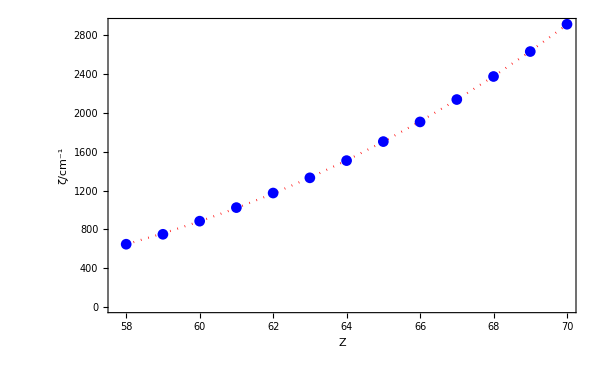

```mathematica
fitDatawithAround=Transpose[{Range[58,70],numCols[[4]]}];
fitData=Transpose[{Range[58,70],Round/@numCols[[4]]}];
model=A(Z-Z0)^m;

fittedζ=FindFit[fitData,{model,A>0,m<2},{{A,640},{Z0,48},{m,2}},Z];
fittedζ
fittedModelζ=model/.fittedζ;
fittedData=Transpose[{Z,fittedModelζ}/.{Z->Range[58,70]}];
nonLinModel=NonlinearModelFit[fitData,{model,A>0},{{A,200},{Z0,56},{m,3}},Z]
nonLinFittedData=Transpose[{Range[58,70],nonLinModel/@Range[58,70]}];
nonLinModel["ParameterTable"]
ListPlot[{fitDatawithAround,nonLinFittedData},{Joined->{False,True}},PlotStyle->{Blue,{Dotted,Red}},Frame->True,FrameStyle->Directive[16],FrameLabel->{"Z","ζ/cm^-1"},ImageSize->600,AspectRatio->1/GoldenRatio]
```

FittedModel[5.82268 (-47.7726+Z)^2]

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
A | 5.82268 | 0.111259 | 52.3344 | 1.52598×10^-14
Z0 | 47.7726 | 0.173833 | 274.819 | 1.85873×10^-22

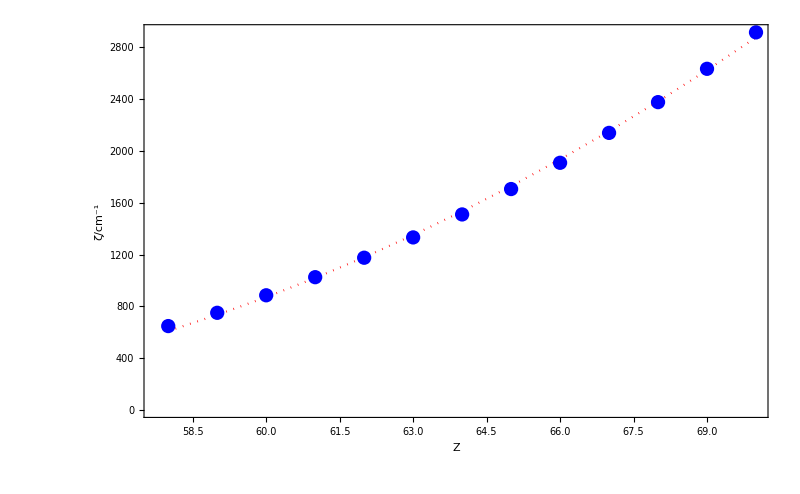

```mathematica
fitDatawithAround=Transpose[{Range[58,70],numCols[[4]]}];
fitData=Transpose[{Range[58,70],Round/@numCols[[4]]}];
model=A(Z-Z0)^2;
nonLinModel=NonlinearModelFit[fitData,{model,A>0},{{A,1},{Z0,50}},Z]
nonLinFittedData=Transpose[{Range[58,70],nonLinModel/@Range[58,70]}];
nonLinModel["ParameterTable"]
ListPlot[{fitDatawithAround,nonLinFittedData},{Joined->{False,True}},PlotStyle->{Blue,{Dotted,Red}},Frame->True,FrameStyle->Directive[16],FrameLabel->{"Z","ζ/cm^-1"},ImageSize->800,AspectRatio->1/GoldenRatio]
```

## Running over the Lanthanide Row, using Carnall1989 as starting values. Using spin-spin. Varying all that was varied and fixing all that was fixed. Including Ce and Yb

```mathematica
Import["inhomConstraints.m"];
```

```mathematica
filePrefix="varied-and-fixed";
filePrevix="trashcan";
σexp=2.0;
Do[(
numE=numE0;
ln=theLanthanides[[numE]];
Print[ln];
pVars=variedSymbols[ln];
constraints=caseConstraints[ln];

carnalKey="appendix:"<>ln<>":RawTable";
expData={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=If[OddQ[numE],
Flatten[Position[Flatten[{#,#}&/@(Last/@Carnall[carnalKey]),1],"not included"]],
Flatten[Position[Last/@Carnall[carnalKey],"not included"]]
];
independentVars=Variables[pVars/.constraints];
startValues=AssociationThread[independentVars,independentVars/.LoadParameters[ln]];
sol=FixingFit[numE,
expData,
excludedDataIndices,
pVars,
startValues,
σexp,
constraints,
"OtherSimplifier"->(("OtherSimplifier"/.Options[ClassicalFit])/.(σSS->_):> (σSS->1)),
"MaxIterations"->1000,
"MaxHistory"->1000,
"FilePrefix"->filePrefix<>"/"<>ln,
"TruncationEnergy"->50000,
"PrintFun"->Print]
),
{numE0,   {2}}
];
Run["~/Scripts/pushover done"];
```

Pr

Using a truncation energy of 50000 K

Determining gaps in the data ...

Retrieving the LSJMJ basis for f^2 ...

Getting reference free-ion parameters for Pr using LaF3 ...

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Using : /Users/juan/ZiaLab/Codebase/qlanth/compiled/Pr-compiled-intermediate-truncated-ham-7085466368566688849.mx

The truncated Hamiltonian has a dimension of 91x91 ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Fitting for 75 data points with 18 free parameters. The effective degrees of freedom are 57 ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Solution found in 1.22475s

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/varied-and-fixed/Pr-sols-86901058-6c34-46cd-92f3-94dc47afc1df.m

```mathematica
sol
```

<|simplifier→{M2→(14 M0)/25,M4→(31 M0)/100,P4→P2/2,P6→P2/10,Bx→0,By→0,Bz→0,B12→0,B14→0,B16→0,B34→0,B36→0,B56→0,S12→0,S14→0,S16→0,S22→0,S24→0,S26→0,S34→0,S36→0,S44→0,S46→0,S56→0,S66→0,T2→0,T3→0,T4→0,T6→0,T7→0,T8→0,T11p→0,T11→0,T12→0,T14→0,T15→0,T16→0,T18→0,T17→0,T19→0,T2p→0,F0→0,P0→0,σSS→1,T11p→0,T11→0,T12→0,T14→0,T15→0,T16→0,T18→0,T17→0,T19→0,T2p→0},freeIonSymbols→{F0,F2,F4,F6,ζ},truncationEnergy→50000,numE→2,expData→{{0.,3H4,0.2},{57.,3H4,71.},{71.,3H4,95.},{136.,3H4,138.},{195.,3H4,183.},{204.,3H4,221.},{322.,3H4,333.},{,3H4,444.},{508.,3H4,463.},{,3H5,2126.},{,3H5,2158.},{2179.,3H5,2191.},{2272.,3H5,2284.},{2299.,3H5,2290.},{2304.,3H5,2295.},{2354.,3H5,2318.},{2412.,3H5,2399.},{2431.,3H5,2412.},{2457.,3H5,2438.},{2567.,3H5,2540.},{,3H6,4179.},{4223.,3H6,4200.},{4268.,3H6,4283.},{4305.,3H6,4321.},{4388.,3H6,4384.},{4440.,3H6,4467.},{,3H6,4478.},{4508.,3H6,4496.},{4529.,3H6,4508.},{4581.,3H6,4590.},{4673.,3H6,4693.},{,3H6,4712.},{4785.,3H6,4814.},{5137.,3F2,5145.},{5182.,3F2,5182.},{5201.,3F2,5185.},{5275.,3F2,5270.},{5280.,3F2,5276.},{6453.,3F3,6456.},{6495.,3F3,6490.},{6499.,3F3,6508.},{6587.,3F3,6579.},{6602.,3F3,6600.},{6622.,3F3,6628.},{6722.,3F3,6740.},{6927.,3F4,6918.},{,3F4,6936.},{6946.,3F4,6950.},{,3F4,6952.},{6946.,3F4,6953.},{6980.,3F4,6983.},{7029.,3F4,7034.},{7104.,3F4,7096.},{7165.,3F4,7152.},{9716.,1G4,9721.},{9751.,1G4,9762.},{9876.,1G4,9860.},{9912.,1G4,9927.},{,1G4,9958.},{10005.,1G4,9996.},{10042.,1G4,10030.},{10163.,1G4,10150.},{10499.,1G4,10516.},{16873.,1D2,16887.},{16893.,1D2,16895.},{17083.,1D2,17082.},{,1D2,17117.},{17183.,1D2,17170.},{20927.,3P0,20911.},{21279.,1I6,21284.},{,1I6,21304.},{21331.,1I6,21340.},{21404.,1I6,21390.},{21418.,1I6,21406.},{,1I6,21481.},{21475.,3P1,21487.},{21522.,3P1,21519.},{,1I6,21570.},{21567.,3P1,21592.},{21585.,1I6,21588.},{,1I6,21637.},{21668.,1I6,21666.},{,1I6,21804.},{21897.,1I6,21889.},{21942.,1I6,21958.},{22691.,3P2,22668.},{22714.,3P2,22704.},{22734.,3P2,22738.},{22772.,3P2,22787.},{22819.,3P2,22817.},{46965.,1S0,46965.}},problemVars→{B02,B04,B06,B22,B24,B26,B44,B46,B66,F2,F4,F6,M0,P2,α,β,γ,ζ},maxIterations→1000,hamDim→91,allVars→{B02,B04,B06,B22,B24,B26,B44,B46,B66,F2,F4,F6,M0,P2,α,β,γ,ζ},freeBies→{2,0,68878.,50347.,32901.,751.7},truncatedDim→91,fittedLevels→75,actualSteps→8,bestRMS→16.1502,solWithUncertainty→{B02→{-220.666,21.9613},B04→{734.537,34.8541},B06→{668.796,49.5284},B22→{-127.279,24.3801},B24→{421.118,52.5595},B26→{-920.465,56.7525},B44→{607.564,32.8165},B46→{-350.718,29.0123},B66→{-789.87,63.4763},F2→{68866.7,27.3857},F4→{50408.,77.2549},F6→{32887.3,61.9188},M0→{1.8707,0.331061},P2→{-40.638,36.3631},α→{16.1451,0.266032},β→{-556.991,16.1965},γ→{1363.81,19.2323},ζ→{749.718,1.01553}},paramSols→{{-221.175,734.572,669.532,-127.339,421.555,-920.137,607.29,-350.317,-789.026,68866.5,50408.6,32886.3,1.87713,-39.9822,16.1394,-556.798,1363.54,749.715},{-220.666,734.514,668.761,-127.24,421.111,-920.445,607.657,-350.683,-789.851,68866.7,50408.,32887.3,1.87068,-40.6607,16.1452,-556.999,1363.82,749.719},{-220.671,734.526,668.8,-127.276,421.124,-920.464,607.567,-350.716,-789.86,68866.7,50408.,32887.3,1.8707,-40.6346,16.1451,-556.991,1363.81,749.718},{-220.667,734.533,668.798,-127.278,421.119,-920.465,607.567,-350.72,-789.867,68866.7,50408.,32887.3,1.87071,-40.65,16.1451,-556.992,1363.81,749.719},{-220.666,734.538,668.796,-127.278,421.118,-920.465,607.565,-350.718,-789.871,68866.7,50408.,32887.3,1.87072,-40.649,16.1451,-556.991,1363.81,749.719},{-220.666,734.538,668.797,-127.279,421.118,-920.464,607.563,-350.715,-789.873,68866.7,50408.,32887.3,1.87069,-40.6338,16.1451,-556.991,1363.81,749.718},{-220.665,734.538,668.797,-127.278,421.119,-920.464,607.564,-350.717,-789.871,68866.7,50408.,32887.3,1.8707,-40.6379,16.1451,-556.991,1363.81,749.718},{-220.666,734.537,668.796,-127.279,421.118,-920.465,607.564,-350.718,-789.87,68866.7,50408.,32887.3,1.8707,-40.638,16.1451,-556.991,1363.81,749.718}},rmsHistory→{16.1516,16.1502,16.1502,16.1502,16.1502,16.1502,16.1502,16.1502},Appendix→<||>,timeTaken/s→1.22475,bestParams→{B02→-220.666,B04→734.537,B06→668.796,B22→-127.279,B24→421.118,B26→-920.465,B44→607.564,B46→-350.718,B66→-789.87,F2→68866.7,F4→50408.,F6→32887.3,M0→1.8707,P2→-40.638,α→16.1451,β→-556.991,γ→1363.81,ζ→749.718}|>

### Plots

```mathematica
ToSubSup[symbol_]:={
{x1,x2,x3}=Characters[ToString[symbol]];
Subsuperscript[x1,x2,x3]
}
FormatWithUncertainty[{val_,delta_}]:=(
FWUtemplate=StringTemplate["`val`(`delta`)"];
FWUtemplate[<|"val"->val,"delta"->delta|>]
);
allVars={F2,F4,F6,ζ,α,β,γ,T2,T3,T4,T6,T7,T8,M0,P2,B02,B04,B06,B22,B24,B26,B44,B46,B66};
billsσ=<|"Ce"->51,"Pr"->16,"Nd"->14,"Pm"->"","Sm"->13,"Eu"->16,"Gd"->10,"Tb"->12,"Dy"->12,"Ho"->10,"Er"->19,"Tm"->10,"Yb"->38|>;
billsn=<|"Ce"->7,"Pr"->75,"Nd"->146,"Pm"->"","Sm"->232,"Eu"->29,"Gd"->70,"Tb"->146,"Dy"->198,"Ho"->204,"Er"->127,"Tm"->56,"Yb"->5|>;
```

```mathematica
folder=FileNameJoin[{NotebookDirectory[],"log",filePrefix}]<>"/*.m";
fnames=FileNames[folder];
fnames=Association@Table[(
ln=StringSplit[StringSplit[fname,"/"][[-1]],"-"][[1]];
ln->Import[fname]
),{fname,fnames}];
fnames=Association[SortBy[Normal[fnames],Position[theLanthanides,#[[1]]][[1]]&]];
```

```mathematica
paramTable=Transpose@Table[
solwithDelta=fnames[ln]["solWithUncertainty"];
numE=Position[theLanthanides,ln][[1,1]];
{#,0}&/@Association[caseConstraints[ln]];
thisCol=(If[Length[#]>0,FormatWithUncertainty[
RoundValueWithUncertainty[#[[1]],#[[2]],"SetPrecision"->True]],#]&/@(allVars/.solwithDelta));
thisCol=If[StringQ[#],#,""]&/@thisCol;
thisCol=Append[thisCol,Round[fnames[ln]["bestRMS"],1]];
thisCol=Append[thisCol,Round[billsσ[ln],1]];
thisCol=Join[thisCol,{Round[fnames[ln]["fittedLevels"]/If[OddQ[numE],2,1]],billsn[ln]}];
constrained=caseConstraints[ln];
thisColCon=(allVars/.constrained)/.fnames[ln]["bestParams"];
thisColCon=If[NumericQ[#],Style["["<>ToString[#]<>"]",Blue],""]&/@thisColCon;
thisColCon=Join[thisColCon,{"","","",""}];
If[Not[#[[1]]==""],Row[{#[[1]]}],Row[{#[[2]]}]]&/@Transpose[{thisCol,thisColCon}]
,
{ln,Keys[fnames]}];
TableForm[paramTable,TableHeadings->{Join[allVars,{"σ","σBill","n","nBill"}],Keys[fnames]}]
```

| Pr | Nd | Sm | Eu | Gd | Tb | Dy | Ho | Er | Tm
F2 | 68860.(20.) | 73020.(30.) | 79700.(200.) | 83000.(100.) | 85640.(10.) | 88870.(20.) | 91830.(40.) | 94560.(30.) | 97570.(20.) | 100100.(100.)
F4 | 50400.(70.) | 52700.(100.) | 57200.(200.) | [59240.2] | [60809.] | [62834.6] | 64350.(30.) | 66480.(40.) | 68050.(40.) | 69600.(300.)
F6 | 32880.(60.) | 35750.(70.) | 40200.(100.) | [42539.9] | 44790.(10.) | 47190.(10.) | 49260.(20.) | 51900.(50.) | 54180.(60.) | 56000.(200.)
ζ | 749.(1.) | 885.(2.) | 1175.(7.) | 1332.(9.) | 1509.(3.) | 1705.(2.) | 1908.(1.) | 2139.(1.) | 2377.(1.) | 2634.(5.)
α | 16.1(0.2) | 21.3(0.3) | 20.3(0.5) | [20.16] | 18.8(0.1) | 18.5(0.1) | 18.2(0.1) | 17.7(0.1) | 17.4(0.1) | 16.9(0.9)
β | -550.(10.) | -580.(10.) | -570.(30.) | [-566.9] | [-600.] | -586.(4.) | -638.(6.) | -615.(8.) | -580.(10.) | -610.(50.)
γ | 1360.(10.) | 1430.(20.) | [1500.] | [1500.] | [1575.] | [1650.] | 1802.(5.) | [1800.] | [1800.] | [1820.]
T2 |  | 290.(10.) | [300.] | [300.] | [300.] | [320.] | 315.(5.) | [400.] | [400.] | [400.]
T3 |  | 30.(10.) | [36.] | [40.] | [42.] | [40.] | 30.(10.) | 36.(8.) | 40.(10.) | 
T4 |  | 50.(10.) | [56.] | [60.] | [62.] | [50.] | 90.(40.) | 96.(7.) | 63.(9.) | 
T6 |  | -280.(20.) | -330.(40.) | [-300.] | [-295.] | -350.(40.) | -290.(40.) | -260.(50.) | -280.(20.) | 
T7 |  | 330.(20.) | 360.(40.) | [370.] | [350.] | 320.(30.) | 370.(20.) | 300.(40.) | 330.(20.) | 
T8 |  | 300.(20.) | 340.(20.) | [320.] | [310.] | 330.(10.) | 320.(20.) | 340.(20.) | 360.(20.) | 
M0 | 1.8(0.3) | 2.1(0.3) | 2.5(0.5) | [2.1] | 3.3(0.1) | 2.4(0.09) | 3.22(0.06) | 2.61(0.08) | 3.8(0.1) | 3.(1.)
P2 | -30.(30.) | 210.(40.) | 300.(100.) | [360.] | 720.(40.) | 390.(20.) | 620.(10.) | 550.(20.) | 680.(20.) | 600.(100.)
B02 | -220.(20.) | -250.(40.) | -200.(200.) | -200.(100.) | [-231.] | -240.(40.) | -230.(20.) | [-240.] | -230.(30.) | -250.(50.)
B04 | 730.(30.) | 500.(100.) | 300.(400.) | 400.(100.) | [604.] | 600.(100.) | 560.(70.) | 500.(100.) | 300.(100.) | 400.(100.)
B06 | 670.(40.) | 600.(100.) | 600.(500.) | 500.(100.) | [280.] | 300.(100.) | 170.(90.) | 300.(100.) | 440.(70.) | 300.(200.)
B22 | -120.(20.) | -50.(40.) | [-50.] | [-50.] | [-99.] | -100.(50.) | -60.(10.) | -100.(20.) | -90.(30.) | -100.(40.)
B24 | 420.(50.) | 500.(100.) | 600.(300.) | [597.] | [340.] | 260.(70.) | 190.(70.) | 240.(60.) | 350.(90.) | 300.(100.)
B26 | -910.(50.) | -800.(100.) | -600.(400.) | [-706.] | [-721.] | -730.(80.) | -670.(50.) | -550.(60.) | -480.(20.) | -400.(100.)
B44 | 600.(30.) | 500.(100.) | 400.(400.) | [408.] | [452.] | 480.(30.) | 550.(30.) | 460.(40.) | 300.(100.) | 400.(100.)
B46 | -350.(20.) | -400.(100.) | -400.(400.) | [-508.] | [-204.] | -240.(80.) | -100.(100.) | -200.(30.) | -230.(30.) | -200.(200.)
B66 | -780.(60.) | -830.(80.) | -700.(400.) | [-692.] | [-509.] | -520.(90.) | -540.(40.) | -580.(30.) | -500.(20.) | -500.(100.)
σ | 16 | 14 | 21 | 22 | 10 | 9 | 11 | 9 | 14 | 17
σBill | 16 | 14 | 13 | 16 | 10 | 12 | 12 | 10 | 19 | 10
n | 75 | 146 | 233 | 29 | 70 | 146 | 198 | 204 | 127 | 56
nBill | 75 | 146 | 232 | 29 | 70 | 146 | 198 | 204 | 127 | 56

## Running over the Lanthanide Row, using Carnall1989 as starting values. Using spin-spin. Varying F2,F4,F6,ζ,α,β,γ,M0,P2,B02,B04,B06,B22,B24,B26,B44,B46,B66

```mathematica
filePrefix="carnall-all-params";
Do[(
cfVars={F2,F4,F6,ζ,α,β,γ,M0,P2,B02,B04,B06,B22,B24,B26,B44,B46,B66};
numE=numE0;
σexp=2.0;
ln=theLanthanides[[numE]];
carnalKey="appendix:"<>ln<>":RawTable";
expData={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=Flatten[Position[Last/@Carnall[carnalKey],"not included"]];
problemVars=cfVars;
startValues=problemVars/.LoadParameters[ln];
sol=ClassicalFit[numE,
expData,
excludedDataIndices,
problemVars,
startValues,
σexp,
"OtherSimplifier"->(("OtherSimplifier"/.Options[ClassicalFit])/.(σSS->_):> (σSS->1)),
"MaxIterations"->1000,
"MaxHistory"->1000,
"FilePrefix"->filePrefix<>"/"<>ln,
"TruncationEnergy"->50000,
"PrintFun"->Print]
),
{numE0,  {2,12,3,11,4,10,5,9,6,8,7}}
];
Run["~/Scripts/pushover done"];
```

```mathematica
ResourceFunction["DarkMode"][False]
```

### Plots

```mathematica
ToSubSup[symbol_]:={
{x1,x2,x3}=Characters[ToString[symbol]];
Subsuperscript[x1,x2,x3]
}
FormatWithUncertainty[{val_,delta_}]:=(
FWUtemplate=StringTemplate["`val`±`delta`"];
FWUtemplate[<|"val"->val,"delta"->delta|>]
)
```

```mathematica
folder=FileNameJoin[{NotebookDirectory[],"log",filePrefix}]<>"/*.m";
```

```mathematica
fnames=FileNames[folder];
fnames=Association@Table[(
ln=StringSplit[StringSplit[fname,"/"][[-1]],"-"][[1]];
ln->Import[fname]
),{fname,fnames}];
fnames=Association[SortBy[Normal[fnames],Position[theLanthanides,#[[1]]][[1]]&]];
```

```mathematica
fittedSymbols=fnames["Pr"]["problemVars"];
```

```mathematica
billsσ=Association@@{"Pr"->16,"Nd"->14,"Pm"->"","Sm"->13,"Eu"->16,"Gd"->10,"Tb"->12,"Dy"->12,"Ho"->10,"Er"->19,"Tm"->10};
```

```mathematica
bills=Transpose[Table[fittedSymbols/.LoadParameters[ln],{ln,Keys[fnames]}]];
```

```mathematica
valsWithσ=<||>;
roundedTable=Table[(
sol=fnames[ln];
fitted={#[[1]],#[[2]]}&/@sol["solWithUncertainty"];
fittedSymbols=First/@fitted;
fittedValues=Last/@fitted;
valsWithσ[ln]=Map[RoundValueWithUncertainty@@#&,fittedValues];
fittedValues=Table[FormatWithUncertainty[RoundValueWithUncertainty[val[[1]],val[[2]],"SetPrecision"->True]],{val,fittedValues}];
σBest=Round[sol["rmsHistory"][[-1]],1.];
fittedSymbols=Join[fittedSymbols,{σ,SuperStar[σ]}];
Join[fittedValues,{ToString[σBest],billsσ[ln]}]
),{ln,Keys[fnames]}];
TableForm[Transpose[roundedTable],TableHeadings->{Row[{#," / cm^-1"}]&/@fittedSymbols,Keys[fnames]}]
```

| Pr | Nd | Pm | Sm | Eu | Gd | Tb | Dy | Ho | Er | Tm
F2 / cm^-1 | 68860.±20. | 73010.±10. | 76400.±30. | 79450.±30. | 90800.±200. | 87900.±20. | 89090.±50. | 91860.±40. | 94490.±30. | 97860.±20. | 100350.±20.
F4 / cm^-1 | 50400.±70. | 52720.±40. | 55060.±40. | 56650.±30. | 106520.±40. | 67300.±20. | 63200.±20. | 64390.±30. | 66330.±40. | 69280.±40. | 70230.±90.
F6 / cm^-1 | 32880.±60. | 35740.±50. | 37760.±50. | 39740.±20. | 53370.±20. | 45910.±10. | 47470.±10. | 49410.±20. | 51860.±50. | 55360.±60. | 56780.±80.
ζ / cm^-1 | 749.±1. | 885.3±0.8 | 1022.±1. | 1173.±1. | 1351.±2. | 1491.±3. | 1707.±2. | 1907.±1. | 2139.±1. | 2374.±1. | 2634.±1.
α / cm^-1 | 16.1±0.2 | 21.3±0.1 | 20.7±0.2 | 19.4±0.1 | 436.±1. | 35.1±0.1 | 19.3±0.1 | 18.4±0.1 | 17.5±0.1 | 17.8±0.1 | 16.7±0.2
β / cm^-1 | -550.±10. | -590.±10. | -567.±8. | -552.±5. | 18762.±7. | 197.±3. | -624.±4. | -638.±6. | -618.±8. | -590.±10. | -600.±10.
γ / cm^-1 | 1360.±10. | 1440.±10. | 1444.±8. | 1694.±4. | -27732.±7. | -814.±2. | 1530.±3. | 1775.±5. | 1838.±9. | 1410.±10. | 1600.±20.
M0 / cm^-1 | 1.8±0.3 | 2.1±0.1 | 2.33±0.07 | 2.59±0.06 | -7.6±0.1 | 2.0±0.1 | 2.5±0.09 | 3.32±0.06 | 2.51±0.08 | 3.5±0.1 | 3.9±0.2
P2 / cm^-1 | -40.±30. | 190.±10. | 280.±10. | 350.±10. | -2280.±30. | 160.±40. | 440.±20. | 640.±10. | 530.±20. | 550.±20. | 710.±40.
B02 / cm^-1 | -220.±20. | -250.±40. | -200.±100. | -200.±30. | -210.±60. | -230.±70. | -230.±40. | -240.±20. | -220.±50. | -230.±30. | -250.±30.
B04 / cm^-1 | 730.±30. | 500.±100. | 460.±90. | 400.±100. | 400.±100. | 600.±300. | 640.±90. | 500.±80. | 500.±100. | 300.±100. | 450.±60.
B06 / cm^-1 | 660.±40. | 620.±50. | 630.±70. | 600.±100. | 500.±100. | 0±300. | 300.±100. | 360.±80. | 300.±100. | 430.±70. | 290.±60.
B22 / cm^-1 | -120.±20. | -50.±30. | -50.±50. | -30.±50. | -50.±40. | -50.±50. | -100.±50. | -60.±20. | -100.±20. | -90.±30. | -100.±20.
B24 / cm^-1 | 420.±50. | 510.±90. | 520.±60. | 570.±50. | 400.±100. | 300.±300. | 260.±70. | 300.±100. | 240.±60. | 360.±90. | 300.±40.
B26 / cm^-1 | -920.±50. | -840.±40. | -730.±20. | -700.±90. | -710.±90. | -1000.±100. | -720.±80. | -600.±50. | -550.±60. | -480.±20. | -440.±20.
B44 / cm^-1 | 600.±30. | 550.±50. | 480.±50. | 380.±60. | 460.±70. | 400.±200. | 460.±30. | 520.±40. | 460.±40. | 300.±100. | 430.±40.
B46 / cm^-1 | -350.±20. | -400.±40. | -440.±60. | -500.±100. | -500.±100. | 300.±200. | -250.±80. | -250.±90. | -190.±30. | -230.±30. | -240.±60.
B66 / cm^-1 | -780.±60. | -820.±30. | -740.±20. | -700.±90. | -480.±90. | -700.±100. | -520.±90. | -530.±40. | -570.±30. | -500.±20. | -490.±30.
σ / cm^-1 | 16. | 13. | 4. | 13. | 10. | 4. | 9. | 12. | 9. | 15. | 11.
σ^* / cm^-1 | 16 | 14 |  | 13 | 16 | 10 | 12 | 12 | 10 | 19 | 10

```mathematica
sorter=fittedSymbols;
```

```mathematica
Length[fittedSymbols]
```

20

```mathematica
rowSlashWithUncertainty=Transpose[Table[Around[#[[1]],#[[2]]]&/@row,{row,Values[valsWithσ]}]];
```

```mathematica
rowSlash=Transpose[Table[First/@row,{row,Values[valsWithσ]}]];
fig2=ListPlot[rowSlashWithUncertainty,
FrameTicks->{Transpose[{Range[1,11],Keys[fnames]}],Automatic},
Frame->True,
FrameLabel->{"","B_q^(k) / cm^-1"},
PlotLegends->fittedSymbols[[;;-3]],
Joined->True,
PlotMarkers->Automatic,
ImageSize->800,
FrameStyle->Directive[Black,15],
PlotLabel->Style["Crystal field parameters in LaF_3 (start Morrison)\n",20,Black],
PlotRange->{{0.9,8.1},{-1000,1000}},
FrameStyle->Directive[15]];
fig2=ColorNegate[Rasterize[Framed[fig2,FrameMargins->40,FrameStyle->White]]]
(*fig2//CopyToClipboard*)
```

-Graphics-

```mathematica
figs=Table[
p=ListPlot[
{((#[[1]]-#[[2]])&)/@rowSlashWithUncertainty[[idx]],
((#[[1]]+#[[2]])&)/@rowSlashWithUncertainty[[idx]]
},
Joined->True,
FrameTicks->{
Transpose[{Range[1,Length[fnames]],Keys[fnames]}],
Automatic},
PlotStyle->Hue[Length[fittedSymbols]/idx],
Filling->{1->{2}},
ImageSize->800,
Frame->True,
PlotRange->{{0.9,8.1},All},
FrameStyle->Directive[Black,15],
FrameLabel->{"",Row[{fittedSymbols[[idx]]," / cm^-1"}]},
Epilog->{Point/@(Transpose[{Range[1,11],bills[[idx]]}]),
{Dotted,Line[(Transpose[{Range[1,11],bills[[idx]]}])]}
}
],
{idx,1,Length[rowSlashWithUncertainty]}];
figs=ColorNegate[Rasterize[Framed[#,FrameMargins->40,FrameStyle->White],ImageResolution->100]]&/@figs;
imDims=ImageDimensions[figs[[1]]];
```

```mathematica
figs=ImageResize[#,imDims]&/@figs;
figs=PadRight[figs,20,ImageResize[Image[{{0,0},{0,0}}],ImageDimensions[figs[[1]]]]];
figs=Partition[figs,4];
```

```mathematica
Export["~/temp/panel2.jpg",ImagePad[ImageAssemble[figs],100,Black]]
```

~/temp/panel2.jpg

```mathematica
fig3=ListPlot[bills,FrameTicks->{Transpose[{Range[1,Length[fnames]],Keys[fnames]}],Automatic},Frame->True,
FrameLabel->{"","B_q^(k) / cm^-1"},
PlotLegends->Flatten[ToSubSup/@fittedSymbols[[;;9]]],
Joined->True,
PlotMarkers->Automatic,
ImageSize->800,
FrameStyle->Directive[Black,15],
PlotLabel->Style["Crystal field parameters in LaF_3 (Carnall)\n",20,Black],
PlotRange->{{0.9,8.1},{-1000,1000}},FrameStyle->Directive[15]];
fig3=ColorNegate[Rasterize[Framed[fig3,FrameMargins->40,FrameStyle->White]]]
```

-Graphics-

```mathematica
Export["~/clyde-vs-bill.gif",Rasterize/@Table[Show[{fig2,fig3}[[Mod[i,2,1]]],ImageSize->800],{i,1,2,1}],"DisplayDurations"->2]
```

~/clyde-vs-bill.gif

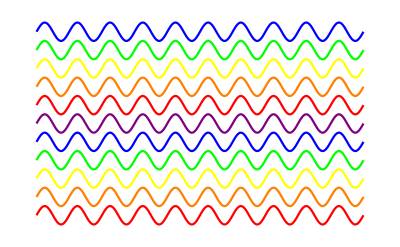

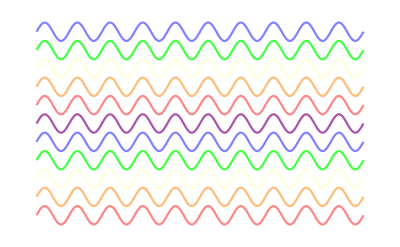

```mathematica
ms={-5,-4,-3,-2,-1,0,1,2,3,4,5};
colors={Red,Orange,Yellow,Green,Blue,Purple};
dimcolors=({Opacity[RandomReal[{0,0.75}]],#}&/@colors);
funs=Table[{0.5Sin[x]+m},{m,ms}];
Plot[funs,{x,0,20π},Axes->None,PlotStyle->colors]
Plot[funs,{x,0,20π},Axes->None,PlotStyle->dimcolors]
```

## Running over the Lanthanide Row, using Carnall1989 as starting values. Using spin-spin.

```mathematica
ResourceFunction["DarkMode"][True]
```

```mathematica
filePrefix="carnall-with-spin-spin";
Do[(
cfVars={B02,B04,B06,B22,B24,B26,B44,B46,B66};
numE=numE0;
σexp=2.0;
ln=theLanthanides[[numE]];
carnalKey="appendix:"<>ln<>":RawTable";
expData={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=Flatten[Position[Last/@Carnall[carnalKey],"not included"]];
problemVars=cfVars;
startValues=problemVars/.LoadParameters[ln];
sol=ClassicalFit[numE,
expData,
excludedDataIndices,
problemVars,
startValues,
σexp,
"OtherSimplifier"->(("OtherSimplifier"/.Options[ClassicalFit])/.(σSS->_):> (σSS->1)),
"MaxIterations"->1000,
"MaxHistory"->1000,
"FilePrefix"->filePrefix<>"/"<>ln,
"TruncationEnergy"->50000,
"PrintFun"->PrintTemporary]
),
{numE0, {2,12,3,11,4,10,5,9,6,8,7}}
];
Run["~/Scripts/pushover done"];
```

### Plots

```mathematica
ToSubSup[symbol_]:={
{x1,x2,x3}=Characters[ToString[symbol]];
Subsuperscript[x1,x2,x3]
}
FormatWithUncertainty[{val_,delta_}]:=(
FWUtemplate=StringTemplate["`val`±`delta`"];
FWUtemplate[<|"val"->val,"delta"->delta|>]
)
```

```mathematica
folder=FileNameJoin[{NotebookDirectory[],"log",filePrefix}]<>"/*.m";
```

```mathematica
fnames=FileNames[folder];
fnames=Association@Table[(
ln=StringSplit[StringSplit[fname,"/"][[-1]],"-"][[1]];
ln->Import[fname]
),{fname,fnames}];
fnames=Association[SortBy[Normal[fnames],Position[theLanthanides,#[[1]]][[1]]&]];
```

```mathematica
fittedSymbols=fnames["Pr"]["problemVars"];
```

```mathematica
billsσ=Association@@{"Pr"->16,"Nd"->14,"Pm"->"","Sm"->13,"Eu"->16,"Gd"->10,"Tb"->12,"Dy"->12,"Ho"->10,"Er"->19,"Tm"->10};
```

```mathematica
bills=Transpose[Table[fittedSymbols[[;;9]]/.LoadParameters[ln],{ln,Keys[fnames]}]];
```

```mathematica
valsWithσ=<||>;
roundedTable=Table[(
sol=fnames[ln];
fitted={#[[1]],#[[2]]}&/@sol["solWithUncertainty"];
fittedSymbols=First/@fitted;
fittedValues=Last/@fitted;
valsWithσ[ln]=Map[RoundValueWithUncertainty@@#&,fittedValues];
fittedValues=Table[FormatWithUncertainty[RoundValueWithUncertainty[val[[1]],val[[2]],"SetPrecision"->True]],{val,fittedValues}];
σBest=Round[sol["rmsHistory"][[-1]],1.];
fittedSymbols=Join[fittedSymbols,{σ,SuperStar[σ]}];
Join[fittedValues,{ToString[σBest],billsσ[ln]}]
),{ln,Keys[fnames]}];
TableForm[Transpose[roundedTable],TableHeadings->{Row[{#," / cm^-1"}]&/@fittedSymbols,Keys[fnames]}]
```

| Pr | Nd | Pm | Sm | Eu | Gd | Tb | Dy | Ho | Er | Tm
B02 / cm^-1 | -210.±20. | -250.±40. | -200.±100. | -180.±60. | -130.±60. | -220.±70. | -90.±60. | -220.±30. | -220.±50. | -230.±30. | -260.±30.
B04 / cm^-1 | 730.±30. | 500.±100. | 450.±90. | 800.±90. | 300.±100. | 500.±300. | 510.±80. | 510.±80. | 600.±100. | 300.±100. | 450.±60.
B06 / cm^-1 | 660.±40. | 590.±50. | 630.±70. | 500.±100. | 100.±100. | -100.±400. | 300.±100. | 100.±90. | 300.±100. | 420.±80. | 300.±60.
B22 / cm^-1 | -120.±20. | -40.±30. | -60.±50. | -50.±40. | -20.±40. | -110.±40. | -90.±60. | -80.±10. | -80.±20. | -90.±30. | -90.±20.
B24 / cm^-1 | 420.±50. | 500.±100. | 510.±60. | 300.±80. | 410.±90. | 200.±200. | 150.±60. | 210.±80. | 200.±60. | 380.±90. | 300.±40.
B26 / cm^-1 | -920.±50. | -840.±40. | -720.±20. | -700.±90. | -1300.±80. | -800.±100. | -760.±80. | -700.±40. | -570.±50. | -490.±20. | -410.±20.
B44 / cm^-1 | 600.±30. | 520.±50. | 480.±50. | 290.±60. | 500.±70. | 500.±200. | 300.±50. | 550.±40. | 450.±40. | 300.±100. | 430.±40.
B46 / cm^-1 | -340.±20. | -390.±50. | -440.±60. | -500.±100. | -1000.±80. | -300.±300. | -350.±90. | -100.±100. | -150.±40. | -240.±30. | -220.±60.
B66 / cm^-1 | -780.±60. | -810.±40. | -740.±20. | -690.±90. | 210.±90. | -200.±500. | -580.±80. | -480.±40. | -540.±30. | -520.±20. | -500.±30.
σ / cm^-1 | 15. | 13. | 4. | 16. | 23. | 20. | 18. | 15. | 12. | 19. | 11.
σ^* / cm^-1 | 16 | 14 |  | 13 | 16 | 10 | 12 | 12 | 10 | 19 | 10

```mathematica
sorter=fittedSymbols;
```

```mathematica
rowSlashWithUncertainty=Transpose[Table[Around[#[[1]],#[[2]]]&/@row,{row,Values[valsWithσ]}]];
```

```mathematica
rowSlash=Transpose[Table[First/@row,{row,Values[valsWithσ]}]];
fig2=ListPlot[rowSlashWithUncertainty,
FrameTicks->{Transpose[{Range[1,11],Keys[fnames]}],Automatic},
Frame->True,
FrameLabel->{"","B_q^(k) / cm^-1"},
PlotLegends->Flatten[ToSubSup/@fittedSymbols[[;;9]]],
Joined->True,
PlotMarkers->Automatic,
ImageSize->800,
FrameStyle->Directive[Black,15],
PlotLabel->Style["Crystal field parameters in LaF_3 (start Morrison)\n",20,Black],
PlotRange->{{0.9,8.1},{-1000,1000}},
FrameStyle->Directive[15]];
fig2=ColorNegate[Rasterize[Framed[fig2,FrameMargins->40,FrameStyle->White]]]
(*fig2//CopyToClipboard*)
```

-Graphics-

```mathematica
figs=Table[
p=ListPlot[
{((#[[1]]-#[[2]])&)/@rowSlashWithUncertainty[[idx]],
((#[[1]]+#[[2]])&)/@rowSlashWithUncertainty[[idx]]
},
Joined->True,
FrameTicks->{
Transpose[{Range[1,Length[fnames]],Keys[fnames]}],
Automatic},
PlotStyle->Hue[9/idx],
Filling->{1->{2}},
ImageSize->800,
Frame->True,
PlotRange->{{0.9,8.1},{-1000,1000}},
FrameStyle->Directive[Black,15],
FrameLabel->{"",Row[{Flatten[ToSubSup/@fittedSymbols[[;;9]]][[idx]]," / cm^-1"}]},
Epilog->{Point/@(Transpose[{Range[1,11],bills[[idx]]}]),
{Dotted,Line[(Transpose[{Range[1,11],bills[[idx]]}])]}
}
],
{idx,1,Length[rowSlashWithUncertainty]}];
figs=ColorNegate[Rasterize[Framed[#,FrameMargins->40,FrameStyle->White],ImageResolution->100]]&/@figs;
figs=Partition[figs,3]
```

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Export["~/temp/panel.jpg",ImagePad[ImageAssemble[figs],100,Black]]
```

~/temp/panel.jpg

```mathematica
fig3=ListPlot[bills,FrameTicks->{Transpose[{Range[1,Length[fnames]],Keys[fnames]}],Automatic},Frame->True,
FrameLabel->{"","B_q^(k) / cm^-1"},
PlotLegends->Flatten[ToSubSup/@fittedSymbols[[;;9]]],
Joined->True,
PlotMarkers->Automatic,
ImageSize->800,
FrameStyle->Directive[Black,15],
PlotLabel->Style["Crystal field parameters in LaF_3 (Carnall)\n",20,Black],
PlotRange->{{0.9,8.1},{-1000,1000}},FrameStyle->Directive[15]];
fig3=ColorNegate[Rasterize[Framed[fig3,FrameMargins->40,FrameStyle->White]]]
```

-Graphics-

```mathematica
Export["~/clyde-vs-bill.gif",Rasterize/@Table[Show[{fig2,fig3}[[Mod[i,2,1]]],ImageSize->800],{i,1,2,1}],"DisplayDurations"->2]
```

~/clyde-vs-bill.gif

```mathematica
ms={-5,-4,-3,-2,-1,0,1,2,3,4,5};
colors={Red,Orange,Yellow,Green,Blue,Purple};
dimcolors=({Opacity[RandomReal[{0,0.75}]],#}&/@colors);
funs=Table[{0.5Sin[x]+m},{m,ms}];
Plot[funs,{x,0,20π},Axes->None,PlotStyle->colors]
Plot[funs,{x,0,20π},Axes->None,PlotStyle->dimcolors]
```

-Graphics-

-Graphics-

## Running over the Lanthanide Row, using Morrison1979 as starting values, and no spin-spin contributions

```mathematica
Do[(
cfVars={B02,B04,B06,B22,B24,B26,B44,B46,B66};
numE=numE0;
σexp=2.0;
ln=theLanthanides[[numE]];
carnalKey="appendix:"<>ln<>":RawTable";
expData={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=Flatten[Position[Last/@Carnall[carnalKey],"not included"]];
problemVars=cfVars;
startValues=Re[cfVars/.morrison[ln]];
sol=ClassicalFit[numE,
expData,
excludedDataIndices,
problemVars,
startValues,
σexp,
"MaxIterations"->10000,
"FilePrefix"->"morrison-"<>ln,
"TruncationEnergy"->50000,
"PrintFun"->Print]
),
{numE0, {(*2,12,3,11,10,*)5,9,6,7}}
];
(*Run["~/Scripts/pushover done"];*)
```

Using a truncation energy of 50000 K

Determining gaps in the data ...

Retrieving the LSJMJ basis for f^5 ...

Getting reference free-ion parameters for Sm using LaF3 ...

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy}). Loading the previously saved compiled function and intermediate coupling basis ...

Using : /Users/juan/ZiaLab/Codebase/qlanth/compiled/Sm-compiled-intermediate-truncated-ham-2412893238857387527.mx

The truncated Hamiltonian has a dimension of 1267x1267 ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Fitting for 467 data points with 9 free parameters. The effective degrees of freedom are 458 ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Solution found in 44.9338s

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/morrison-Sm-sols-05596575-8394-42b5-8091-074c89173a35.m

Using a truncation energy of 50000 K

Determining gaps in the data ...

Retrieving the LSJMJ basis for f^9 ...

Getting reference free-ion parameters for Dy using LaF3 ...

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy}). Loading the previously saved compiled function and intermediate coupling basis ...

Using : /Users/juan/ZiaLab/Codebase/qlanth/compiled/Dy-compiled-intermediate-truncated-ham-4408876277833367877.mx

The truncated Hamiltonian has a dimension of 983x983 ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Fitting for 396 data points with 9 free parameters. The effective degrees of freedom are 387 ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Solution found in 29.1375s

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/morrison-Dy-sols-d919fd4c-7886-4b6c-beea-f13fcfab59c2.m

Using a truncation energy of 50000 K

Determining gaps in the data ...

Retrieving the LSJMJ basis for f^6 ...

Getting reference free-ion parameters for Eu using LaF3 ...

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy}). Loading the previously saved compiled function and intermediate coupling basis ...

Using : /Users/juan/ZiaLab/Codebase/qlanth/compiled/Eu-compiled-intermediate-truncated-ham-411786770890005432.mx

The truncated Hamiltonian has a dimension of 1129x1129 ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Fitting for 29 data points with 9 free parameters. The effective degrees of freedom are 20 ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of FindMinimum::sszero will be suppressed during this calculation.

Solution found in 25.6316s

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/morrison-Eu-sols-e2b79c52-4243-4669-920d-ab6c34f546c4.m

Using a truncation energy of 50000 K

Determining gaps in the data ...

Retrieving the LSJMJ basis for f^7 ...

Getting reference free-ion parameters for Gd using LaF3 ...

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy}). Loading the previously saved compiled function and intermediate coupling basis ...

Using : /Users/juan/ZiaLab/Codebase/qlanth/compiled/Gd-compiled-intermediate-truncated-ham-3936091488839025389.mx

The truncated Hamiltonian has a dimension of 189x189 ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Fitting for 140 data points with 9 free parameters. The effective degrees of freedom are 131 ...

Starting the fitting process ...

Solution found in 0.819516s

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/morrison-Gd-sols-e3a48fbf-2733-4302-baf6-30eb313de10a.m

## Running over the Lanthanide Row, using Carnall as the starting values, and no spin-spin contributions

```mathematica
Do[(
cfVars={B02,B04,B06,B22,B24,B26,B44,B46,B66};
numE=numE0;
σexp=2.0;
ln=theLanthanides[[numE]];
carnalKey="appendix:"<>ln<>":RawTable";
expData={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=Flatten[Position[Last/@Carnall[carnalKey],"not included"]];
problemVars=cfVars;
startValues=problemVars/.LoadParameters[ln];
sol=ClassicalFit[numE,
expData,
excludedDataIndices,
problemVars,
startValues,
σexp,
"MaxIterations"->10000,
"TruncationEnergy"->50000,
"PrintFun"->Print]
),
{numE0,{2,12,3,11,4,10,5,9,6,8,7}}
];
(*Run["~/Scripts/pushover done"];*)
```

## N at a time

```mathematica
Get["misc.m"]
```

```mathematica
numE=2;
ln=theLanthanides[[numE]];
maxHistory=100;
maxIterations=10;
numReps=1;
cfVars={B02, B04, B06, B22, B24, B26, B44, B46, B66};
problemVars={B02, B04, B06, B22, B24, B26, B44, B46, B66};
standardValues={-218.,738.,679.,-120.,431.,-921.,616.,-348.,-788.,68878.,50347.,32901.,2.08,-88.6,16.23,-566.6,1371.,751.7};
PrintFun=Print;
σexp=2;
```

```mathematica
allVars/.LoadParameters["Pr"]
```

allVars

```mathematica
carnalKey = "appendix:" <> ln <> ":RawTable";
expData = {#[[3]], #[[1]], #[[4]]} & /@ Carnall[carnalKey];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=Flatten[Position[Last/@ Carnall[carnalKey],"not included"]];
(*remove the indices for data not included in fitting *)
presentDataIndices=Complement[presentDataIndices,excludedDataIndices];
```

```mathematica
(* I need to define the function that returns the sorted eigenvalues of x *)
(* for definining the squared difference I shall use an iterator that runs over the good indices, I think that what NMinimize expects for LM should allow for this initially I will do this with the full Hamiltonian *)
ham=HamMatrixAssembly[numE];
simplifier={
F0->0,
M2->0.56 M0,
M4->0.31M0,
P4->0.4 P2,
P6->0.1 P2,
B12->0,B14->0,B16->0,B34->0,B36->0,B56->0,
S12->0,S14->0,S16->0,S22->0,S24->0,S26->0,S34->0,S36->0,
S44->0,S46->0,S56->0,S66->0,T11p->0,T11->0,T12->0,T14->0,T15->0,
T16->0,T18->0,T17->0,T19->0,T2p->0,σSS->0};
ham=ReplaceInSparseArray[ham,simplifier];
allVars=Variables[Normal[ham]];
(*compile the hamiltonian with all variables*)
compiledHam=Compile[Evaluate[allVars],Evaluate[N[Normal[ham]]]];
```

```mathematica
(* using the problemVars I need to create the argument list with NumericQ*)
problemVarsQ=(ToString[#]<>"_?NumericQ")&/@problemVars;
problemVarsQString=StringJoin[Riffle[problemVarsQ,", "]];
(* I also need to have the padded arguments with the variables in the right position and the fixed values in the remaining ones *)
problemVarsPositions=Position[allVars,#][[1,1]]&/@problemVars;
problemVarsString=StringJoin[Riffle[ToString/@problemVars,", "]];
varsWithConstants=standardValues;
varsWithConstants[[problemVarsPositions]] = problemVars;
varsWithConstantsString=ToString[varsWithConstants];
(* I need to define now the function that *)
Clear[HamSortedEigenvalues];
hamEigenvaluesTemplate=StringTemplate["
HamSortedEigenvalues[`problemVarsQ`]:=(
ham=compiledHam@@`varsWithConstants`;
eigenValues = Sort@Eigenvalues@ham;
eigenValues = eigenValues - Min[eigenValues];
HamSortedEigenvalues[`problemVarsString`] = eigenValues;
Return[eigenValues]
)"];
hamString=hamEigenvaluesTemplate[<|
"problemVarsQ"->problemVarsQString,
"varsWithConstants"->varsWithConstantsString,
"problemVarsString"->problemVarsString
 |>];
ToExpression[hamString];
costFuncTemplate=StringTemplate["
PartialHamEigenvalues[`problemVarsQ`][i_]:=(
eigenVals = HamSortedEigenvalues[`problemVarsString`];
eigenVals[[i]]
)
"];
costFuncString=costFuncTemplate[<|"problemVarsQ"->problemVarsQString,
"problemVarsString"->problemVarsString
|>];
ToExpression[costFuncString];
```

```mathematica
startValues=Re[problemVars/.morrison[ln]];
startValues=problemVars/.LoadParameters["Pr"];
history={};
problemVarsWithStartValues=Transpose[{problemVars,startValues}];
fmSol=FindMinimum[
Sum[(expData[[j]][[1]]-(PartialHamEigenvalues@@problemVars)[j])^2,{j,presentDataIndices}],
problemVarsWithStartValues,
Method->"LevenbergMarquardt",
MaxIterations->100000,
EvaluationMonitor:>(
history=Append[history,problemVars]
)
];
```

```mathematica
solVec=Last/@fmSol[[-1]];
fullSolVec=standardValues;
fullSolVec[[problemVarsPositions]]=solVec;
PrintFun["Calculating the numerical hamiltonian of the solution ..."];
fullHam=compiledHam@@fullSolVec;
PrintFun["Calculating energies and eigenvectors ..."];
{eigenEnergies,eigenVectors}=Eigensystem[fullHam];
states=Transpose[{eigenEnergies,eigenVectors}];
states=SortBy[states,First];
eigenEnergies=First/@states;
PrintFun["Shifting energies to make ground state zero of energy ..."];
eigenEnergies=eigenEnergies-eigenEnergies[[1]];
states=Transpose[{eigenEnergies,Last/@states}];
```

Calculating the numerical hamiltonian of the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

```mathematica
(*PrintFun["Calculating the quadratic approximation to each eigenvalue ... "]
allVarsVec=Transpose[{allVars}];
p0=Transpose[{fullSolVec}];
linMat={};
quadMat={};
Table[(
aVarPosition=Position[allVars,aVar][[1,1]];
isolationValues=ConstantArray[0,Length[allVars]];
isolationValues[[aVarPosition]]=1;
perHam=compiledHam@@isolationValues;
lin=FirstOrderPerturbation[First/@states,Last/@states,perHam];
quad=SecondOrderPerturbation[First/@states,Last/@states,perHam];
linMat=Append[linMat,lin];
quadMat=Append[quadMat,quad];
),
{aVar, problemVars}
];
PrintFun["Transposing derivative matrices into columns ..."]
linMat=Transpose[linMat];
quadMat=Transpose[quadMat];*)

PrintFun["Calculating the eigenvalue vector at solution ..."]
λ0Vec=Transpose[{eigenEnergies[[presentDataIndices]]}];
PrintFun["Putting together the experimental vector ..."]
λexp=Transpose[{First/@expData[[presentDataIndices]]}];
```

Calculating the quadratic approximation to each eigenvalue ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

```mathematica
(λ0Vec-λexp)
```

{{-0.2},{0.733599},{0.18551},{-0.0390499},{-0.267283},{-0.00359881},{0.970028},{0.307813},{0.500422},{-0.0314925},{-0.798709},{0.481039},{-0.237374},{-0.11515},{-0.474073},{-0.139816},{-0.1123},{-0.605776},{0.0128187},{-0.337821},{-0.55139},{-0.142717},{0.0941018},{-0.298981},{-0.305996},{0.00201579},{-0.498362},{-0.9065},{-0.427839},{-0.465704},{-0.783051},{-0.956203},{-0.15898},{0.547996},{-0.236847},{-0.652837},{-0.650045},{0.683859},{0.0782522},{-0.600706},{0.148407},{0.430186},{0.231963},{0.363956},{-0.0176059},{0.277776},{0.158663},{0.298312},{0.93642},{0.805358},{0.628339},{0.809889},{0.494585},{-0.26393},{-0.113955},{-0.692574},{-0.790135},{-1.03033},{-0.84146},{-0.283473},{-0.126977},{-0.140645},{-0.0438853},{0.139319},{0.36832},{0.591187},{-0.00680393},{-3.55668},{-0.252929},{-0.152769},{-0.26933},{0.313507},{0.292118},{0.156402},{-1.34547},{-1.13696},{0.534845},{-2.81189},{2.45948},{0.325738},{0.528441},{-0.128175},{-0.208145},{-0.560834},{2.13666},{2.24123},{1.40082},{0.876211},{1.54674},{-0.361821}}

```mathematica
chosenVar
```

B66

```mathematica
Get["misc.m"]
```

```mathematica
PrintFun["Calculating the quadratic approximation to each eigenvalue ... "]
allVarsVec=Transpose[{allVars}];
p0=Transpose[{fullSolVec}];
linMat={};
quadMat={};
Table[(
aVarPosition=Position[allVars,aVar][[1,1]];
isolationValues=ConstantArray[0,Length[allVars]];
isolationValues[[aVarPosition]]=1;
perHam=compiledHam@@isolationValues;
(*Print[MatrixPlot[perHam]];*)
lin=FirstOrderPerturbation[Last/@states,perHam];
quad=SecondOrderPerturbation[First/@states,Last/@states,perHam];
linMat=Append[linMat,lin];
quadMat=Append[quadMat,quad];
),
{aVar, problemVars}
];
PrintFun["Transposing derivative matrices into columns ..."]
linMat=Transpose[linMat];
quadMat=Transpose[quadMat];
```

Calculating the quadratic approximation to each eigenvalue ...

Transposing derivative matrices into columns ...

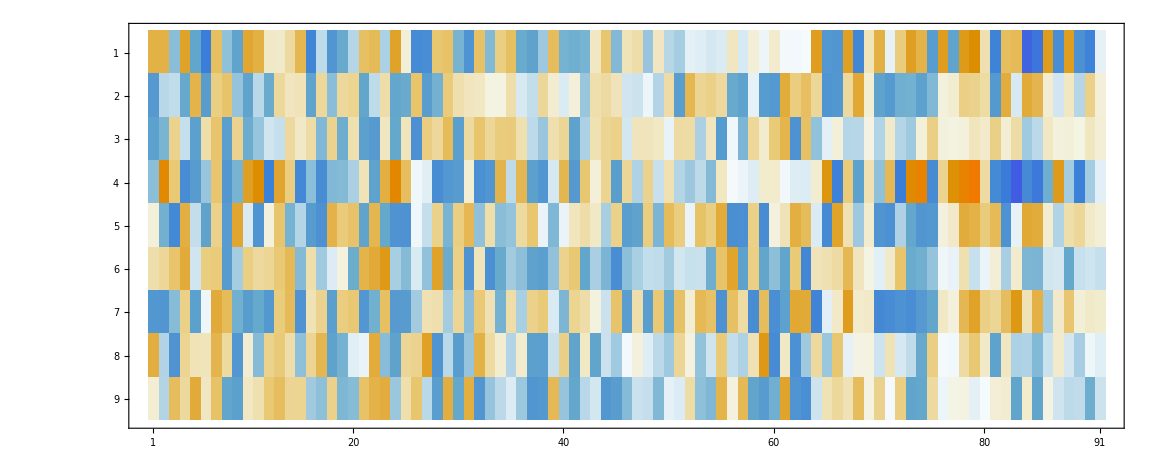

```mathematica
MatrixPlot[Transpose[linMat]]
```

```mathematica
linMatT=Transpose[linMat];
linMatT=(#-#[[1]])&/@linMatT;
linMat=Transpose[linMatT];
```

```mathematica
(*Table[(
aVar=problemVars[[varIdx]];
paramBest=aVar/.fmSolAssoc;
othersFixed=AssociationThread[Delete[problemVars,varIdx]->Delete[solVec,varIdx]];
thisPoly=sqdiff/.othersFixed;
polySols=Last/@Last/@Solve[thisPoly==minpoly+1*totalVariance];
polySols=Select[polySols,Im[#]==0&];
paramSigma=Max[polySols]-Min[polySols];
(aVar->{paramBest,paramSigma})
),
{varIdx,1,Length[problemVars]}];*)

(*{constant,grad,hess}=FromPolynomialToSecondOrder[sqdiff,problemVars];*)
```

```mathematica
simplisqdiff/.{B66^2->5 B66^2}
```

{204607.+520.102 B66+3.3062 B66^2}

```mathematica
λ0Vec
```

{{0.},{71.7336},{95.1855},{137.961},{182.733},{220.996},{333.97},{444.308},{2126.5},{2157.97},{2190.2},{2284.48},{2289.76},{2294.88},{2317.53},{2398.86},{2411.89},{2437.39},{2540.01},{4178.66},{4199.45},{4282.86},{4321.09},{4383.7},{4466.69},{4478.},{4495.5},{4507.09},{4589.57},{4692.53},{4711.22},{4813.04},{5144.84},{5182.55},{5184.76},{5269.35},{5275.35},{6456.68},{6490.08},{6507.4},{6579.15},{6600.43},{6628.23},{6740.36},{6917.98},{6936.28},{6950.16},{6952.3},{6953.94},{6983.81},{7034.63},{7096.81},{7152.49},{9720.74},{9761.89},{9859.31},{9926.21},{9956.97},{9995.16},{10029.7},{10149.9},{10515.9},{16887.},{16895.1},{17082.4},{17117.6},{17170.},{20907.4},{21283.7},{21303.8},{21339.7},{21390.3},{21406.3},{21481.2},{21485.7},{21517.9},{21570.5},{21589.2},{21590.5},{21637.3},{21666.5},{21803.9},{21888.8},{21957.4},{22670.1},{22706.2},{22739.4},{22787.9},{22818.5},{46964.6}}

```mathematica
sqdiff
```

{6.93423×10^9+366.762 B02+1.51202 B02^2-1327.64 B04-0.192675 B02 B04+0.282997 B04^2+285.891 B06-0.022234 B02 B06-0.0137977 B04 B06+0.15913 B06^2+1019.46 B22+1.36115 B02 B22-0.246126 B04 B22-0.0777906 B06 B22+2.72676 B22^2+1819.92 B24-0.287584 B02 B24+0.225146 B04 B24-0.0281981 B06 B24-0.375832 B22 B24+0.536711 B24^2+735.813 B26+0.219907 B02 B26-0.128238 B04 B26-0.13264 B06 B26+0.0440767 B22 B26-0.0101825 B24 B26+0.37487 B26^2-2229.92 B44-0.152633 B02 B44+0.268812 B04 B44+0.0689779 B06 B44-0.493725 B22 B44+0.288428 B24 B44-0.0207652 B26 B44+0.643596 B44^2-1472.51 B46+0.0928816 B02 B46-0.0457809 B04 B46+0.00203781 B06 B46-0.00472607 B22 B46-0.049911 B24 B46+0.00964018 B26 B46+0.0387331 B44 B46+0.303052 B46^2-317.23 B66+0.00496721 B02 B66+0.0651513 B04 B66-0.0137675 B06 B66+0.0563993 B22 B66-0.0464329 B24 B66+0.216932 B26 B66-0.252221 B44 B66+0.095259 B46 B66+0.33062 B66^2}

```mathematica
λexp
```

{{0.2},{71.},{95.},{138.},{183.},{221.},{333.},{444.},{2126.},{2158.},{2191.},{2284.},{2290.},{2295.},{2318.},{2399.},{2412.},{2438.},{2540.},{4179.},{4200.},{4283.},{4321.},{4384.},{4467.},{4478.},{4496.},{4508.},{4590.},{4693.},{4712.},{4814.},{5145.},{5182.},{5185.},{5270.},{5276.},{6456.},{6490.},{6508.},{6579.},{6600.},{6628.},{6740.},{6918.},{6936.},{6950.},{6952.},{6953.},{6983.},{7034.},{7096.},{7152.},{9721.},{9762.},{9860.},{9927.},{9958.},{9996.},{10030.},{10150.},{10516.},{16887.},{16895.},{17082.},{17117.},{17170.},{20911.},{21284.},{21304.},{21340.},{21390.},{21406.},{21481.},{21487.},{21519.},{21570.},{21592.},{21588.},{21637.},{21666.},{21804.},{21889.},{21958.},{22668.},{22704.},{22738.},{22787.},{22817.},{46965.}}

```mathematica
λexp
```

{{0.2},{71.},{95.},{138.},{183.},{221.},{333.},{444.},{2126.},{2158.},{2191.},{2284.},{2290.},{2295.},{2318.},{2399.},{2412.},{2438.},{2540.},{4179.},{4200.},{4283.},{4321.},{4384.},{4467.},{4478.},{4496.},{4508.},{4590.},{4693.},{4712.},{4814.},{5145.},{5182.},{5185.},{5270.},{5276.},{6456.},{6490.},{6508.},{6579.},{6600.},{6628.},{6740.},{6918.},{6936.},{6950.},{6952.},{6953.},{6983.},{7034.},{7096.},{7152.},{9721.},{9762.},{9860.},{9927.},{9958.},{9996.},{10030.},{10150.},{10516.},{16887.},{16895.},{17082.},{17117.},{17170.},{20911.},{21284.},{21304.},{21340.},{21390.},{21406.},{21481.},{21487.},{21519.},{21570.},{21592.},{21588.},{21637.},{21666.},{21804.},{21889.},{21958.},{22668.},{22704.},{22738.},{22787.},{22817.},{46965.}}

```mathematica
linMat[[presentDataIndices]]//Dimensions
```

{90,9}

```mathematica
diff/.fmSol[[2]]
```

{-0.2,0.733599,0.18551,-0.0390499,-0.267283,-0.00359881,0.970028,0.307813,0.500422,-0.0314925,-0.798709,0.481039,-0.237374,-0.11515,-0.474073,-0.139816,-0.1123,-0.605776,0.0128187,-0.337821,-0.55139,-0.142717,0.0941018,-0.298981,-0.305996,0.00201579,-0.498362,-0.9065,-0.427839,-0.465704,-0.783051,-0.956203,-0.15898,0.547996,-0.236847,-0.652837,-0.650045,0.683859,0.0782522,-0.600706,0.148407,0.430186,0.231963,0.363956,-0.0176059,0.277776,0.158663,0.298312,0.93642,0.805358,0.628339,0.809889,0.494585,-0.26393,-0.113955,-0.692574,-0.790135,-1.03033,-0.84146,-0.283473,-0.126977,-0.140645,-0.0438853,0.139319,0.36832,0.591187,-0.00680393,-3.55668,-0.252929,-0.152769,-0.26933,0.313507,0.292118,0.156402,-1.34547,-1.13696,0.534845,-2.81189,2.45948,0.325738,0.528441,-0.128175,-0.208145,-0.560834,2.13666,2.24123,1.40082,0.876211,1.54674,-0.361821}

```mathematica
FromPolynomialToSecondOrder[sqdiff,problemVars][[-1]]//MatrixForm
```

(5.36811 | -2.14125 | -1.42229 | 0.6925 | -0.184409 | 0.61691 | -2.23372 | 2.63458 | 0.0894767
-2.14125 | 2.18566 | 1.15004 | 0.309603 | 0.139662 | -0.458276 | 1.9986 | -2.15869 | -0.00521721
-1.42229 | 1.15004 | 1.15448 | 0.321578 | -0.089828 | -0.369759 | 1.31196 | -1.51605 | -0.0642402
0.6925 | 0.309603 | 0.321578 | 5.64418 | -0.405055 | -0.069183 | 0.099778 | -0.729792 | 0.0322067
-0.184409 | 0.139662 | -0.089828 | -0.405055 | 1.07739 | 0.00733295 | 0.197178 | 0.062096 | -0.0424735
0.61691 | -0.458276 | -0.369759 | -0.069183 | 0.00733295 | 0.816975 | -0.373252 | 0.440102 | 0.231228
-2.23372 | 1.9986 | 1.31196 | 0.099778 | 0.197178 | -0.373252 | 3.13458 | -2.21788 | -0.327394
2.63458 | -2.15869 | -1.51605 | -0.729792 | 0.062096 | 0.440102 | -2.21788 | 3.36204 | 0.186837
0.0894767 | -0.00521721 | -0.0642402 | 0.0322067 | -0.0424735 | 0.231228 | -0.327394 | 0.186837 | 0.664187)

```mathematica
2*Transpose[linMat[[presentDataIndices]]].linMat[[presentDataIndices]]//MatrixForm
```

(5.36811 | -2.14125 | -1.42229 | 0.6925 | -0.184409 | 0.61691 | -2.23372 | 2.63458 | 0.0894767
-2.14125 | 2.18566 | 1.15004 | 0.309603 | 0.139662 | -0.458276 | 1.9986 | -2.15869 | -0.00521721
-1.42229 | 1.15004 | 1.15448 | 0.321578 | -0.089828 | -0.369759 | 1.31196 | -1.51605 | -0.0642402
0.6925 | 0.309603 | 0.321578 | 5.64418 | -0.405055 | -0.069183 | 0.099778 | -0.729792 | 0.0322067
-0.184409 | 0.139662 | -0.089828 | -0.405055 | 1.07739 | 0.00733295 | 0.197178 | 0.062096 | -0.0424735
0.61691 | -0.458276 | -0.369759 | -0.069183 | 0.00733295 | 0.816975 | -0.373252 | 0.440102 | 0.231228
-2.23372 | 1.9986 | 1.31196 | 0.099778 | 0.197178 | -0.373252 | 3.13458 | -2.21788 | -0.327394
2.63458 | -2.15869 | -1.51605 | -0.729792 | 0.062096 | 0.440102 | -2.21788 | 3.36204 | 0.186837
0.0894767 | -0.00521721 | -0.0642402 | 0.0322067 | -0.0424735 | 0.231228 | -0.327394 | 0.186837 | 0.664187)

Calculating the sum of squares of differences around solution ...

B02

Calculating the difference between eigenvalues at solution ...

127355.+1169.03 B02+2.68406 B02^2

B04

Calculating the difference between eigenvalues at solution ...

127355.+1169.03 B02+2.68406 B02^2

B06

Calculating the difference between eigenvalues at solution ...

596080.-1614.12 B04+1.09283 B04^2

B22

Calculating the difference between eigenvalues at solution ...

266149.-783.826 B06+0.577239 B06^2

B24

Calculating the difference between eigenvalues at solution ...

40215.3+673.248 B22+2.82209 B22^2

B26

Calculating the difference between eigenvalues at solution ...

99989.8-464.028 B24+0.538694 B24^2

B44

Calculating the difference between eigenvalues at solution ...

346630.+752.512 B26+0.408487 B26^2

B46

Calculating the difference between eigenvalues at solution ...

598413.-1936.79 B44+1.56729 B44^2

B66

Calculating the difference between eigenvalues at solution ...

203110.+1168.47 B46+1.68102 B46^2

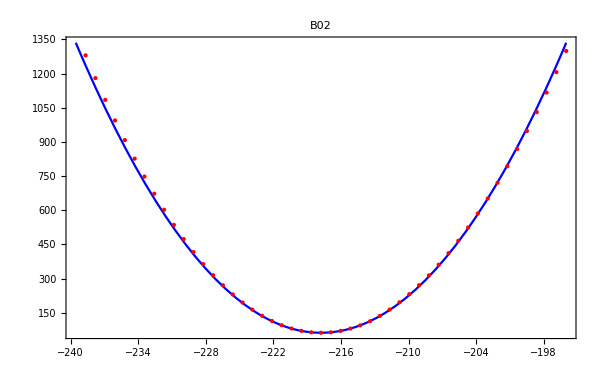
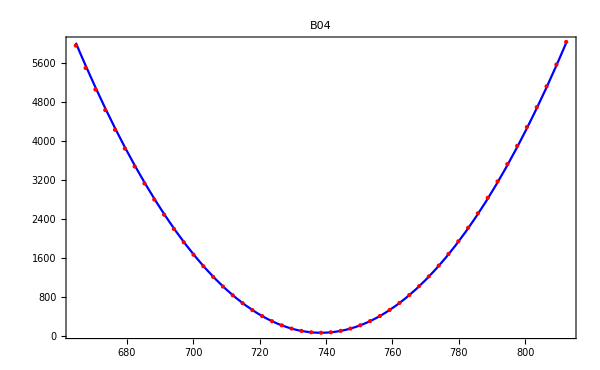
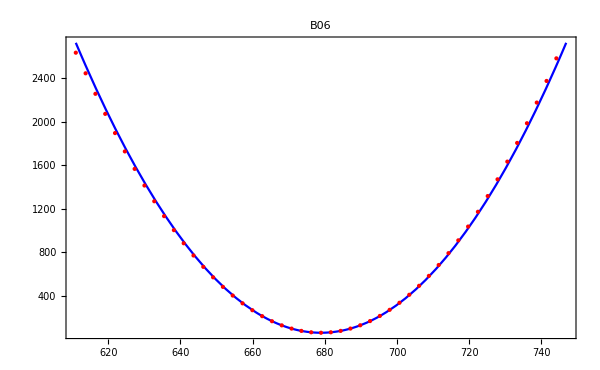
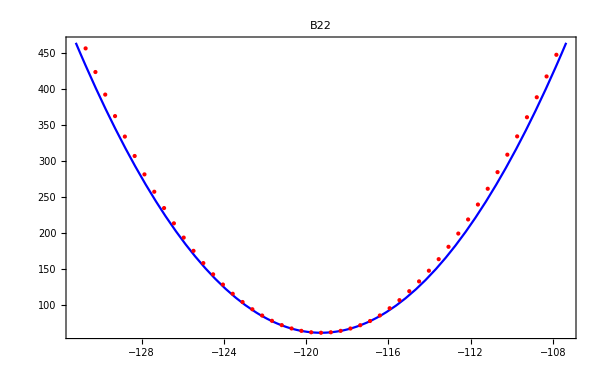
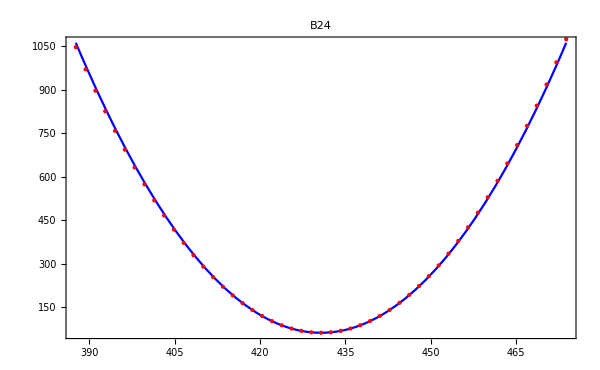
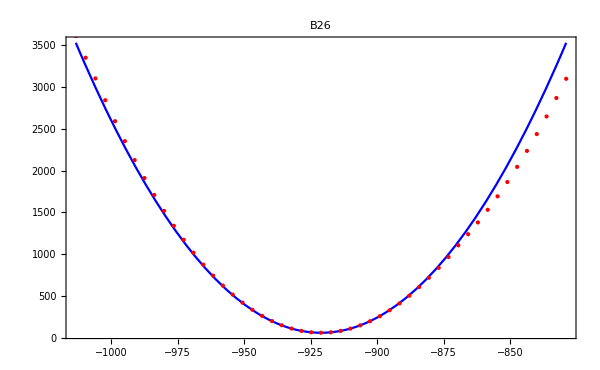
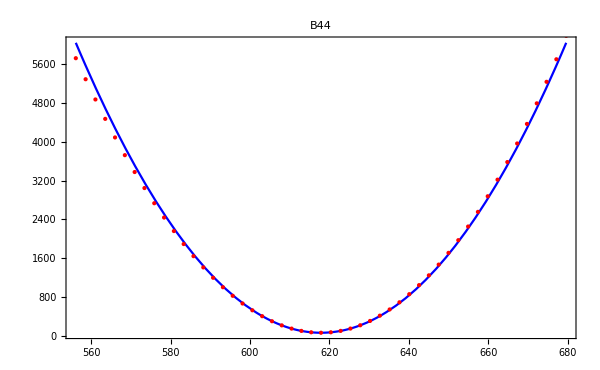
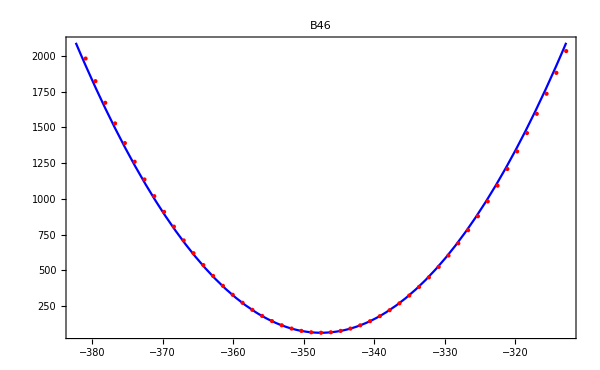

```mathematica
λexp=Transpose[{First/@expData[[presentDataIndices]]}];
λ0Vec=Transpose[{eigenEnergies[[presentDataIndices]]}];
λ0Vec=λ0Vec-Min[λ0Vec];
solVec=Last/@fmSol[[-1]];
problemVarsVec=Transpose[{problemVars}];
solVecVec=Transpose[{solVec}];
fmSolAssoc=Association[fmSol[[2]]];
(*totalVariance=Length[presentDataIndices]*σexp^2;*)
linearEigenValues=Expand[λ0Vec+linMat[[presentDataIndices]].(problemVarsVec-solVecVec)];
diff=Flatten[linearEigenValues-λexp];
PrintFun["Calculating the sum of squares of differences around solution ... "];
sqdiff=Expand[Total[diff^2]];
plots=Table[(
chosenVar=problemVars[[testVarIdx]];
Print[chosenVar];
{paramMin,paramMax}=MinMax[{0.90solVec[[testVarIdx]],1.10solVec[[testVarIdx]]}];
PrintFun["Calculating the difference between eigenvalues at solution ..."];
(*diff=(λ0Vec-λexp)+linMat[[presentDataIndices]].(problemVarsVec-solVecVec)+quadMat[[presentDataIndices]].(Map[#^2&,(problemVarsVec-solVecVec)]);*)
(*diff=(λ0Vec-λexp)+linMat[[presentDataIndices]].(problemVarsVec-solVecVec)+1*quadMat[[presentDataIndices]].(Map[#^2&,(problemVarsVec-solVecVec)]);*)

(*Print["Calculating the minimum (which should coincide to sol) ..."];
minpoly=sqdiff/.AssociationThread[cfVars->solVec];*)
Print[simplisqdiff];
otherVars=Complement[problemVars,{chosenVar}];
simpler=(AssociationThread[otherVars->(otherVars/.fmSol[[2]])]);
simplisqdiff=sqdiff/.simpler;
(*Print[simplisqdiff];*)
testRange=Subdivide[paramMin,paramMax,50];
(*simplisqdiff=simplisqdiff/.{chosenVar^2->1.0*(chosenVar+solVec[[testVarIdx]])^2};*)
plotArg={chosenVar,Min[testRange],Max[testRange]};
numerical=Table[(
repVars=problemVars/.fmSol[[2]];
repVars[[testVarIdx]]=testValue;
theSum=(Sum[(expData[[j]][[1]]-(PartialHamEigenvalues@@repVars)[j])^2,{j,presentDataIndices}]);
{testValue,theSum}
),{testValue,testRange}];

plot1=Plot[simplisqdiff,
plotArg,
PlotStyle->Blue,
Frame->True,
PlotRange->{All,All},
PlotLabel->chosenVar,
FrameStyle->Directive[16],
PlotLegends->Style["linear",Blue],
Epilog->{Red,Point[numerical]},ImageSize->600]
)
,{testVarIdx,1,9}];
plots
```

```mathematica
Rasterize[Grid[Partition[plots,3]]]//CopyToClipboard
```

```mathematica
(*Table[(
aVar=problemVars[[varIdx]];
paramBest=aVar/.fmSolAssoc;
othersFixed=AssociationThread[Delete[problemVars,varIdx]->Delete[solVec,varIdx]];
thisPoly=sqdiff/.othersFixed;
polySols=Last/@Last/@Solve[thisPoly==minpoly+1*totalVariance];
polySols=Select[polySols,Im[#]==0&];
paramSigma=Max[polySols]-Min[polySols];
(aVar->{paramBest,paramSigma})
),
{varIdx,1,Length[problemVars]}]*)
```

```mathematica
solVec=Last/@fmSol[[-1]];
fullSolVec=standardValues;
fullSolVec[[problemVarsPositions]]=solVec;
PrintFun["Calculating the numerical hamiltonian of the solution ..."];
fullHam=compiledHam@@fullSolVec;
PrintFun["Calculating energies and eigenvectors ..."];
{eigenEnergies,eigenVectors}=Eigensystem[fullHam];
eigenEnergies=Sort[eigenEnergies];
(*eigenEnergies=eigenEnergies-Min[eigenEnergies];*)
```

Calculating the numerical hamiltonian of the solution ...

Calculating energies and eigenvectors ...

```mathematica
vareigen={};
lineigen={};
solVec=Last/@fmSol[[-1]];
problemVarIndex=1;
points={solVec[[problemVarIndex]],0.9*solVec[[problemVarIndex]],1.10*solVec[[problemVarIndex]]};
testRange=Subdivide[Min[points],Max[points],50];
Do[(
B02val=testRange[[idx]];
fullSolVec=standardValues;
fullSolVec[[problemVarsPositions]]=solVec;
fullSolVec[[problemVarIndex]]=B02val;
fullHam=compiledHam@@fullSolVec;
directEigen=Sort[Eigenvalues[fullHam]];
(*directEigen=directEigen-Min[directEigen];*)
directEigen={B02val,#}&/@directEigen;
vareigen=Append[vareigen,directEigen];
linearEigen=Table[linMat[[idx]][[problemVarIndex]](B02val-solVec[[problemVarIndex]])+eigenEnergies[[idx]],{idx,1,91}];
lineigen=Append[lineigen,{B02val,#}&/@linearEigen]
)
,{idx,1,Length[testRange]}];
Manipulate[ListPlot[{#[[idx]]&/@vareigen,#[[idx]]&/@lineigen},PlotStyle->{Blue,Red}],{idx,1,Length[vareigen],1}]
```

```mathematica
numsumHere=Total[((#-Min[#]-Flatten[λexp])^2)]&/@Transpose[Transpose[Map[Last,vareigen,{2}]][[presentDataIndices]]];
linsumHere=Total[((#-Min[#]-Flatten[λexp])^2)]&/@Transpose[Transpose[Map[Last,lineigen,{2}]][[presentDataIndices]]];
```

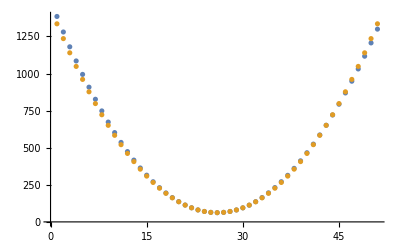

```mathematica
ListPlot[{numsumHere,linsumHere}]
```

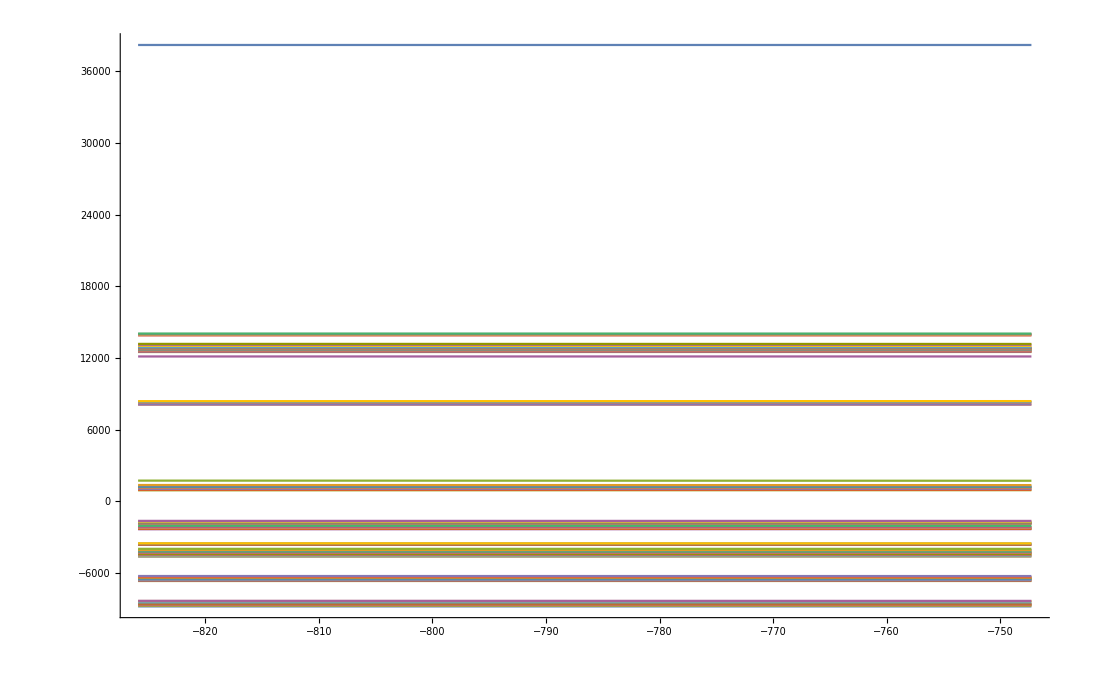

```mathematica
ListPlot[Transpose[lineigen],Joined->True]
```

```mathematica
linMat
```

```mathematica
linearEigen
```

-8811.01

```mathematica
linMat[[1]]*(B02val-solVec[[1]])
```

{14.9471,-8.63865,-7.14875,6.3548,-0.726584,2.06544,-6.50458,7.69003,-0.667852}

-8811.01

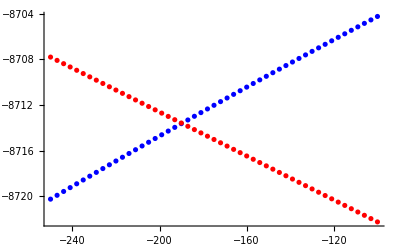

```mathematica
linearEigen
```

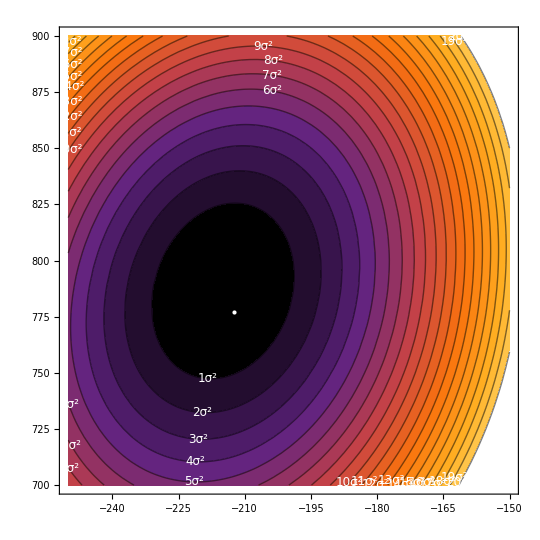

```mathematica
numContours=20;
totalVariance=Length[presentDataIndices]*σexp^2;
contourLevels=(minpoly+(totalVariance*Range[1,numContours]));
contourLabels=ToString/@Range[1,numContours];
contourLabelFunction=(Text[Style[contourLabels[[Position[contourLevels,Nearest[contourLevels,#3][[1]]][[1,1]]]]<>"σ^2",12,FontFamily->"Times",White],{#1,#2}]&);
thisPoly=sqdiff/.AssociationThread[{B06,B22,B24,B26,B44,B46,B66}->solVec[[3;;]]];

ContourPlot[thisPoly,{B02,-250,-150},{B04,700,900},Epilog->{White,Point[solVec[[;;2]]]},ColorFunction->"SunsetColors",
Contours->contourLevels,ContourLabels->contourLabelFunction]
```

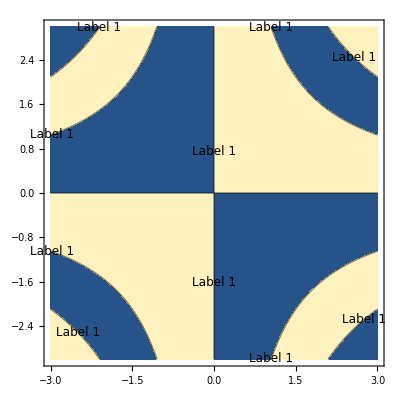

```mathematica
(*Define the function to be contoured*)f[x_,y_]:=Sin[x y]

(*Define a list of custom labels*)
customLabels={"Label 1","Label 2","Label 3","Label 4","Label 5"};

(*Determine the contour levels for the custom labels*)
(*For this example,I'm generating them automatically.*)
(*Replace this with your specific contour levels if needed.*)
contourLevels=Table[f[0,pi*(i-1)/4],{i,Length[customLabels]}];

(*Create a function to map contour levels to custom labels*)
contourLabelFunction=(Text[Style[customLabels[[Position[contourLevels,Nearest[contourLevels,#3][[1]]][[1,1]]]],12,FontFamily->"Times"],{#1,#2}]&);

(*Create the contour plot with custom labels*)
ContourPlot[f[x,y],{x,-3,3},{y,-3,3},Contours->contourLevels,ContourLabels->contourLabelFunction]
```

Function::fpct: Too many parameters in {x,y,z,n} to be filled from Function[{x,y,z,n},Text[customLabels⟦n⟧,{x,y}]][-1.88685,-2.04756,-0.66].

Function::fpct: Too many parameters in {x,y,z,n} to be filled from Function[{x,y,z,n},Text[customLabels⟦n⟧,{x,y}]][2.99546,-0.808113,-0.66].

Function::fpct: Too many parameters in {x,y,z,n} to be filled from Function[{x,y,z,n},Text[customLabels⟦n⟧,{x,y}]][-0.808113,2.99546,-0.66].

General::stop: Further output of Function::fpct will be suppressed during this calculation.

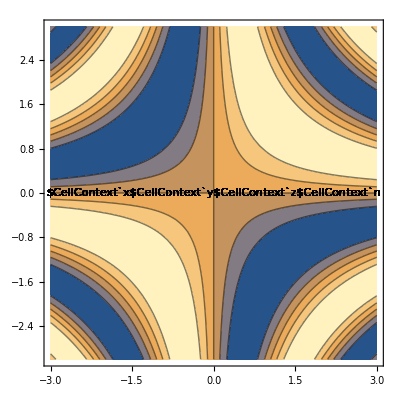

```mathematica
(*Define the function to be contoured*)f[x_,y_]:=Sin[x y]

(*Define a list of custom labels*)
customLabels={"Label 1","Label 2","Label 3","Label 4","Label 5"};

(*Create the contour plot with custom labels*)
ContourPlot[f[x,y],{x,-3,3},{y,-3,3},Contours->Length[customLabels],(*Ensure the number of contours matches the number of labels*)ContourLabels->(Function[{x,y,z,n},Text[Style[customLabels[[n]],12,FontFamily->"Times"],{x,y}]])]
```

```mathematica
(ToString[#]&/@Range[0,numContours])
```

{0,1,2,3,4,5,6,7,8,9,10}

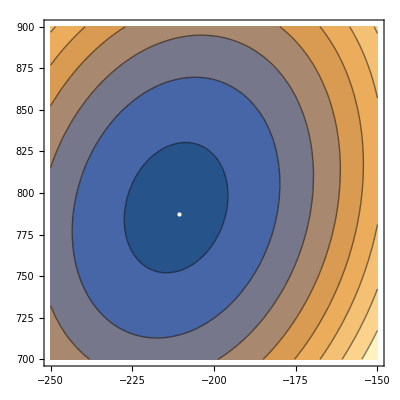

```mathematica
ContourPlot[poly/.AssociationThread[{B06,B22,B24,B26,B44,B46,B66}->solVec[[3;;]]],{B02,-250,-150},{B04,700,900},Epilog->{White,Point[solVec[[;;2]]]}]
```

```mathematica
Length[solVec[[3;;]]]
```

7

```mathematica
(*Define your multivariate polynomial*)polynomial=x^3+x^2 y+x y^2+y^3;

(*Truncate the polynomial to a given order,say 2*)
truncatedPolynomial=Normal[Series[polynomial,{x,0,2},{y,0,2}]];

(*The result is the polynomial truncated to second order*)
truncatedPolynomial
```

x^2 y+x y^2

```mathematica
(*Example usage*)
polynomial=x+x^3+x^2 y+x y^2+y^3;
truncatedPolynomial=truncatePolynomial[polynomial,1];  (*Truncate to total order 2*)

truncatedPolynomial
```

x

```mathematica
Series[sqdiff,problemVars]
```

```mathematica
standardValues[[Flatten[Position[allVars,#]&/@irrelevantVars]]]
```

{68878.,50347.,32901.,2.08,-88.6,16.23,-566.6,1371.,751.7}

```mathematica
Series[sqdiff,{B02,0,2},{B04,0,2},{B06,0,2}]
```

(((2.15421×10^12+9.72449×10^6 B22+38980.9 B22^2+0.224514 B22^3+0.000502353 B22^4-904862. B24-9.76352 B22 B24-0.0428709 B22^2 B24+1319.42 B24^2+0.0101926 B22 B24^2+0.0000461146 B22^2 B24^2-0.0032736 B24^3+1.94318×10^-6 B24^4+208609. B26+0.219615 B22 B26+0.0020445 B22^2 B26-0.147709 B24 B26+0.000487869 B24^2 B26+67.887 B26^2+0.00021744 B22 B26^2+1.52722×10^-6 B22^2 B26^2-0.000117155 B24 B26^2+3.13889×10^-7 B24^2 B26^2+0.00071652 B26^3+1.94487×10^-7 B26^4-190004. B44-2.75445 B22 B44-0.0134615 B22^2 B44+0.565396 B24 B44-0.00109171 B24^2 B44-1.40782 B26 B44-0.000727668 B26^2 B44+519.877 B44^2+0.00239613 B22 B44^2+0.0000123283 B22^2 B44^2-0.000597191 B24 B44^2+1.27729×10^-6 B24^2 B44^2+0.00136219 B26 B44^2+7.0156×10^-7 B26^2 B44^2-0.00358077 B44^3+1.71919×10^-6 B44^4+31123.7 B46-0.424032 B22 B46-0.00154299 B22^2 B46-0.0921977 B24 B46+0.000100985 B24^2 B46-0.188737 B26 B46-0.0000645381 B26^2 B46-0.287868 B44 B46+0.000348783 B44^2 B46+24.3524 B46^2+0.000253203 B22 B46^2+2.21871×10^-6 B22^2 B46^2-0.000502923 B24 B46^2+6.03055×10^-7 B24^2 B46^2+0.000219058 B26 B46^2+1.90671×10^-7 B26^2 B46^2-0.00132725 B44 B46^2+1.3413×10^-6 B44^2 B46^2+0.00131082 B46^3+1.50259×10^-6 B46^4-54972.3 B66-0.0105602 B22 B66+0.000959208 B22^2 B66-0.0287417 B24 B66+0.000427083 B24^2 B66+0.68929 B26 B66+0.000293375 B26^2 B66-0.569526 B44 B66+0.000404065 B44^2 B66+0.00597912 B46 B66+0.000327467 B46^2 B66-24.6398 B66^2-0.0000932539 B22 B66^2+2.37699×10^-7 B22^2 B66^2-0.0000601659 B24 B66^2+4.55565×10^-7 B24^2 B66^2+0.00063031 B26 B66^2+3.54613×10^-7 B26^2 B66^2-0.00050994 B44 B66^2+4.91876×10^-7 B44^2 B66^2-0.0000445915 B46 B66^2+3.21826×10^-7 B46^2 B66^2+0.000843971 B66^3+4.39096×10^-7 B66^4-6.47777×10^7 F2-146.245 B22 F2-0.58566 B22^2 F2+13.563 B24 F2-0.0198011 B24^2 F2-3.1398 B26 F2-0.00102219 B26^2 F2+2.91596 B44 F2-0.00784723 B44^2 F2-0.495042 B46 F2-0.000469247 B46^2 F2+0.83347 B66 F2+0.000379449 B66^2 F2+959.897 F2^2+0.00107078 B22 F2^2+4.28288×10^-6 B22^2 F2^2-0.000100195 B24 F2^2+1.45424×10^-7 B24^2 F2^2+0.0000230361 B26 F2^2+8.11062×10^-9 B26^2 F2^2-0.0000217336 B44 F2^2+5.75162×10^-8 B44^2 F2^2+3.41884×10^-6 B46 F2^2+3.65726×10^-9 B46^2 F2^2-5.7312×10^-6 B66 F2^2-2.00549×10^-9 B66^2 F2^2-0.00711144 F2^3+2.59998×10^-8 F2^4-2.89805×10^6 F4-6.37934 B22 F4-0.0256908 B22^2 F4+0.441504 B24 F4-0.000660113 B24^2 F4-0.155498 B26 F4+0.0000108446 B26^2 F4+0.161104 B44 F4-0.000322771 B44^2 F4-0.10139 B46 F4-0.000214909 B46^2 F4+0.0272923 B66 F4+0.0000871482 B66^2 F4+43.5619 F2 F4-0.000316024 F2^2 F4+30.9279 F4^2+0.0000653212 B22 F4^2+2.62645×10^-7 B22^2 F4^2-4.2805×10^-6 B24 F4^2+7.20988×10^-9 B24^2 F4^2+2.03955×10^-6 B26 F4^2+5.52702×10^-10 B26^2 F4^2-2.82377×10^-6 B44 F4^2+4.49974×10^-9 B44^2 F4^2+1.44663×10^-6 B46 F4^2+3.76801×10^-9 B46^2 F4^2+2.73141×10^-7 B66 F4^2-1.02805×10^-10 B66^2 F4^2-0.00044491 F2 F4^2+3.24834×10^-9 F2^2 F4^2-0.0000288317 F4^3+1.55425×10^-10 F4^4-1.19079×10^8 F6-270.172 B22 F6-1.08121 B22^2 F6+25.6209 B24 F6-0.0370419 B24^2 F6-5.77514 B26 F6-0.00205756 B26^2 F6+5.32789 B44 F6-0.0144152 B44^2 F6-0.845546 B46 F6-0.000469869 B46^2 F6+1.53629 B66 F6+0.000509089 B66^2 F6+1790.85 F2 F6-0.0130975 F2^2 F6+78.3844 F4 F6-0.000804809 F4^2 F6+3456.97 F6^2+0.00409976 B22 F6^2+0.0000164056 B22^2 F6^2-0.000389079 B24 F6^2+5.61671×10^-7 B24^2 F6^2+0.0000866573 B26 F6^2+3.01522×10^-8 B26^2 F6^2-0.0000796206 B44 F6^2+2.17281×10^-7 B44^2 F6^2+0.0000126639 B46 F6^2+6.3042×10^-9 B46^2 F6^2-0.0000239626 B66 F6^2-8.97003×10^-9 B66^2 F6^2-0.027162 F2 F6^2+1.98629×10^-7 F2^2 F6^2-0.00118852 F4 F6^2+1.22005×10^-8 F4^2 F6^2-0.0500724 F6^3+3.79677×10^-7 F6^4-2.70815×10^7 M0-85.6294 B22 M0-0.397794 B22^2 M0+15.7986 B24 M0-0.0232255 B24^2 M0-0.530993 B26 M0+0.00205373 B26^2 M0-4.40537 B44 M0-0.00286656 B44^2 M0+6.47174 B46 M0+0.0189486 B46^2 M0+10.2417 B66 M0+0.00681662 B66^2 M0+416.85 F2 M0-0.00304134 F2^2 M0-17.3567 F4 M0+0.000168258 F4^2 M0+857.97 F6 M0-0.0130333 F6^2 M0+1.37943×10^7 M0^2+31.5336 B22 M0^2+0.126435 B22^2 M0^2-2.98864 B24 M0^2+0.00437074 B24^2 M0^2+0.695311 B26 M0^2+0.000290971 B26^2 M0^2-0.639247 B44 M0^2+0.00168969 B44^2 M0^2+0.0431222 B46 M0^2+0.000101983 B46^2 M0^2-0.136426 B66 M0^2+9.60019×10^-6 B66^2 M0^2-207.445 F2 M0^2+0.00151763 F2^2 M0^2-9.05147 F4 M0^2+0.0000935967 F4^2 M0^2-382.299 F6 M0^2+0.0057972 F6^2 M0^2-97.1493 M0^3+22.2645 M0^4+78996.7 P2+0.155818 B22 P2+0.00052547 B22^2 P2-0.0143249 B24 P2+3.05364×10^-6 B24^2 P2+0.000546298 B26 P2-6.29033×10^-6 B26^2 P2-0.0316547 B44 P2+0.0000373972 B44^2 P2+0.00202537 B46 P2+0.0000196989 B46^2 P2-0.0679207 B66 P2-0.000039359 B66^2 P2-1.29058 F2 P2+8.37637×10^-6 F2^2 P2-0.165761 F4 P2+1.17611×10^-6 F4^2 P2-1.86782 F6 P2+0.0000295602 F6^2 P2-3.55899 M0 P2+0.172028 M0^2 P2+99.5932 P2^2+0.00022831 B22 P2^2+9.24633×10^-7 B22^2 P2^2-0.0000212124 B24 P2^2+3.2187×10^-8 B24^2 P2^2+6.54368×10^-6 B26 P2^2+3.59257×10^-9 B26^2 P2^2-4.54979×10^-6 B44 P2^2+1.25367×10^-8 B44^2 P2^2+7.83423×10^-7 B46 P2^2+2.03099×10^-9 B46^2 P2^2-4.04435×10^-7 B66 P2^2+1.44978×10^-9 B66^2 P2^2-0.00149933 F2 P2^2+1.10026×10^-8 F2^2 P2^2-0.0000623884 F4 P2^2+6.95106×10^-10 F4^2 P2^2-0.00277172 F6 P2^2+4.20721×10^-8 F6^2 P2^2-0.00146046 M0 P2^2+0.000324446 M0^2 P2^2-6.89405×10^-6 P2^3+1.43256×10^-9 P2^4-3.01964×10^9 α-6802.06 B22 α-27.1506 B22^2 α+645.926 B24 α-0.939644 B24^2 α-128.753 B26 α-0.0523904 B26^2 α+131.334 B44 α-0.375198 B44^2 α-6.58522 B46 α-0.0123017 B46^2 α+35.6472 B66 α-0.00131464 B66^2 α+45354.5 F2 α-0.33209 F2^2 α+1957.67 F4 α-0.020243 F4^2 α+83739.3 F6 α-1.26956 F6^2 α+21113.8 M0 α-9686.72 M0^2 α-53.9137 P2 α-0.0702571 P2^2 α+9.53029×10^7 α^2+214.093 B22 α^2+0.856522 B22^2 α^2-20.3827 B24 α^2+0.0293611 B24^2 α^2+4.47734 B26 α^2+0.00155336 B26^2 α^2-4.1414 B44 α^2+0.0113189 B44^2 α^2+0.619076 B46 α^2+0.000302342 B46^2 α^2-1.267 B66 α^2-0.00049113 B66^2 α^2-1416.91 F2 α^2+0.0103606 F2^2 α^2-61.9498 F4 α^2+0.00063504 F4^2 α^2-2611.44 F6 α^2+0.039606 F6^2 α^2-664.394 M0 α^2+302.431 M0^2 α^2+1.69176 P2 α^2+0.00218956 P2^2 α^2-66213.5 α^3+1033.02 α^4+4.37095×10^6 β+11.7984 B22 β+0.0478146 B22^2 β-1.20803 B24 β+0.00140587 B24^2 β+0.810475 B26 β+0.0000413059 B26^2 β-1.27464 B44 β+0.00123755 B44^2 β+0.570756 B46 β+0.000629657 B46^2 β-0.0477515 B66 β-0.000440072 B66^2 β-68.3871 F2 β+0.000500673 F2^2 β-4.68265 F4 β+0.0000446933 F4^2 β-124.149 F6 β+0.00188291 F6^2 β-62.5177 M0 β+14.9414 M0^2 β-0.00312249 P2 β+0.0000909376 P2^2 β-28.5923 α β+98.2282 α^2 β+1723.11 β^2+0.00370261 B22 β^2+0.0000148094 B22^2 β^2-0.000282346 B24 β^2+4.50188×10^-7 B24^2 β^2+0.000101954 B26 β^2+4.17724×10^-8 B26^2 β^2-0.00012464 B44 β^2+2.3461×10^-7 B44^2 β^2+0.0000289079 B46 β^2+1.33363×10^-7 B46^2 β^2+9.57533×10^-6 B66 β^2+1.02804×10^-8 B66^2 β^2-0.024958 F2 β^2+1.82266×10^-7 F2^2 β^2-0.00138915 F4 β^2+1.45957×10^-8 F4^2 β^2-0.045326 F6 β^2+6.8752×10^-7 F6^2 β^2+0.00815501 M0 β^2+0.00532903 M0^2 β^2+0.0000532941 P2 β^2+3.85018×10^-8 P2^2 β^2-1.14577 α β^2+0.0358824 α^2 β^2+0.00225534 β^3+3.83073×10^-7 β^4-2.31002×10^7 γ-49.8537 B22 γ-0.199648 B22^2 γ+4.41051 B24 γ-0.00663763 B24^2 γ+0.0157523 B26 γ+0.0000953954 B26^2 γ-0.511397 B44 γ-0.00150541 B44^2 γ+0.559093 B46 γ+0.00121652 B46^2 γ+0.556943 B66 γ+0.000233405 B66^2 γ+344.104 F2 γ-0.00251676 F2^2 γ+14.2895 F4 γ-0.000148383 F4^2 γ+636.237 F6 γ-0.00964925 F6^2 γ+117.351 M0 γ-72.6931 M0^2 γ-0.36046 P2 γ-0.000547132 P2^2 γ+19748.6 α γ-502.84 α^2 γ+128.447 β γ-0.00825242 β^2 γ+9554.02 γ^2+0.0213421 B22 γ^2+0.0000853923 B22^2 γ^2-0.00201072 B24 γ^2+2.90591×10^-6 B24^2 γ^2+0.000451451 B26 γ^2+1.51635×10^-7 B26^2 γ^2-0.000429779 B44 γ^2+1.13935×10^-6 B44^2 γ^2+0.0000783449 B46 γ^2+6.66745×10^-8 B46^2 γ^2-0.000121187 B66 γ^2-5.28303×10^-8 B66^2 γ^2-0.141415 F2 γ^2+1.03399×10^-6 F2^2 γ^2-0.00628607 F4 γ^2+6.45949×10^-8 F4^2 γ^2-0.260488 F6 γ^2+3.95062×10^-6 F6^2 γ^2-0.0632016 M0 γ^2+0.0301598 M0^2 γ^2+0.000177164 P2 γ^2+2.18555×10^-7 P2^2 γ^2-6.60314 α γ^2+0.206062 α^2 γ^2+0.0099441 β γ^2+3.61323×10^-6 β^2 γ^2-0.0501266 γ^3+0.0000102833 γ^4-3.65231×10^7 ζ-80.926 B22 ζ-0.316699 B22^2 ζ+6.44418 B24 ζ-0.010917 B24^2 ζ-2.28807 B26 ζ-0.00392267 B26^2 ζ+0.093701 B44 ζ-0.00319522 B44^2 ζ+3.61397 B46 ζ-0.00232094 B46^2 ζ-2.99949 B66 ζ-0.00492632 B66^2 ζ+545.04 F2 ζ-0.00400825 F2^2 ζ+19.8386 F4 ζ-0.000192983 F4^2 ζ+989.798 F6 ζ-0.0149836 F6^2 ζ-1821.84 M0 ζ-127.428 M0^2 ζ+8.60373 P2 ζ-0.000916227 P2^2 ζ+25360.7 α ζ-788.968 α^2 ζ-41.4448 β ζ-0.0180344 β^2 ζ+157.632 γ ζ-0.0772662 γ^2 ζ+24625.3 ζ^2+0.0528682 B22 ζ^2+0.000213628 B22^2 ζ^2-0.00304208 B24 ζ^2+6.68663×10^-6 B24^2 ζ^2+0.00217698 B26 ζ^2+2.92219×10^-6 B26^2 ζ^2-0.0013805 B44 ζ^2+3.50686×10^-6 B44^2 ζ^2-0.00176188 B46 ζ^2+3.75467×10^-6 B46^2 ζ^2+0.00102962 B66 ζ^2+2.78611×10^-6 B66^2 ζ^2-0.358594 F2 ζ^2+2.64731×10^-6 F2^2 ζ^2-0.0180346 F4 ζ^2+2.03119×10^-7 F4^2 ζ^2-0.650342 F6 ζ^2+9.83642×10^-6 F6^2 ζ^2+0.388428 M0 ζ^2+0.0832171 M0^2 ζ^2-0.00158011 P2 ζ^2+6.66661×10^-7 P2^2 ζ^2-16.6061 α ζ^2+0.515027 α^2 ζ^2+0.0380798 β ζ^2+0.0000131126 β^2 ζ^2-0.0978533 γ ζ^2+0.0000513934 γ^2 ζ^2-0.756617 ζ^3+0.000234883 ζ^4)+(-97859.7-0.237894 B22-0.000713667 B22^2+0.257017 B24-0.000476259 B24^2-0.269839 B26-0.000137481 B26^2+0.137086 B44-0.0000527756 B44^2+0.0862431 B46-0.000204824 B46^2-0.635531 B66-0.00058387 B66^2+1.48286 F2-0.0000114603 F2^2+0.0563976 F4-1.10529×10^-6 F4^2+2.69512 F6-0.0000402184 F6^2-6.97564 M0-0.391353 M0^2+0.0286568 P2-3.45294×10^-6 P2^2+83.0844 α-2.11168 α^2+0.304012 β-0.0000835664 β^2+0.617274 γ-0.000209965 γ^2+7.38617 ζ-0.00439546 ζ^2) B06+(56.6231+0.000354732 B22+1.49307×10^-6 B22^2-0.000271304 B24+4.15496×10^-7 B24^2+0.000200004 B26+1.31523×10^-7 B26^2-0.000237192 B44+1.86343×10^-7 B44^2+0.0000811349 B46+3.84531×10^-7 B46^2+0.000481235 B66+4.42337×10^-7 B66^2-0.000853504 F2+6.52497×10^-9 F2^2-0.0000216637 F4+6.96547×10^-10 F4^2-0.00158263 F6+2.33293×10^-8 F6^2+0.0046906 M0+0.000220343 M0^2-0.0000106132 P2+2.38097×10^-9 P2^2-0.0456823 α+0.0012092 α^2-0.0000690165 β+4.48222×10^-8 β^2-0.000102743 γ+1.21044×10^-7 γ^2-0.00359729 ζ+2.33309×10^-6 ζ^2) B06^2+O[B06]^3)+((374738.+1.14527 B22+0.00588277 B22^2-0.0775632 B24+0.000110931 B24^2+0.0697154 B26-0.0000291823 B26^2+0.579644 B44-0.000475193 B44^2-0.188278 B46-0.000406958 B46^2-0.00181432 B66-0.000137924 B66^2-5.65345 F2+0.0000418622 F2^2-0.355833 F4+3.41327×10^-6 F4^2-10.5047 F6+0.000160059 F6^2+4.04499 M0+1.19157 M0^2+0.0236794 P2+8.18885×10^-6 P2^2-234.666 α+8.37886 α^2+1.42357 β+0.000156799 β^2-1.07962 γ+0.000845826 γ^2-1.96347 ζ+0.00161317 ζ^2)+0.147057 B06-0.00011353 B06^2+O[B06]^3) B04+((-155.571-0.0000521374 B22+8.96485×10^-8 B22^2-0.000116141 B24+2.72488×10^-7 B24^2+0.0000289907 B26+9.32308×10^-8 B26^2-0.000451239 B44+4.88575×10^-7 B44^2+0.0000387628 B46+1.68742×10^-7 B46^2+0.0000923052 B66+1.41931×10^-7 B66^2+0.00232652 F2-1.68748×10^-8 F2^2+0.000207026 F4-1.80745×10^-9 F4^2+0.00421034 F6-6.42785×10^-8 F6^2-0.00494339 M0-0.000460117 M0^2-9.32059×10^-6 P2-3.20051×10^-9 P2^2+0.0927644 α-0.00335195 α^2-0.00041327 β-7.03946×10^-8 β^2+0.000822165 γ-3.44153×10^-7 γ^2-0.0000864862 ζ-1.07483×10^-7 ζ^2)-0.0000898762 B06+6.95066×10^-8 B06^2+O[B06]^3) B04^2+O[B04]^3)+(((2.55567×10^6+7.45199 B22+0.027408 B22^2-1.33806 B24+0.0017167 B24^2+0.281251 B26+0.000152926 B26^2-0.825402 B44+0.000979498 B44^2-0.106934 B46-0.0000617617 B46^2+0.171289 B66+0.000297347 B66^2-38.4009 F2+0.00028021 F2^2-1.70998 F4+0.0000171318 F4^2-70.7766 F6+0.00107483 F6^2-35.5938 M0+8.30916 M0^2+0.0534008 P2+0.0000605881 P2^2-1801.62 α+56.1698 α^2+2.43273 β+0.000965192 β^2-13.7964 γ+0.00559867 γ^2-18.5791 ζ+0.0132179 ζ^2)-0.239348 B06+0.000179429 B06^2+O[B06]^3)+0.00704056 B04+0.0000714109 B04^2+O[B04]^3) B02+(((5067.62+0.015135 B22+0.0000640628 B22^2-0.00328713 B24+4.51171×10^-6 B24^2+0.0000774979 B26+2.46415×10^-7 B26^2-0.00140231 B44+2.17644×10^-6 B44^2-0.000114245 B46+3.40638×10^-7 B46^2+0.000164855 B66+5.26083×10^-7 B66^2-0.0761322 F2+5.56471×10^-7 F2^2-0.00335288 F4+3.42005×10^-8 F4^2-0.14054 F6+2.13251×10^-6 F6^2-0.0749343 M0+0.0165837 M0^2+6.16172×10^-6 P2+1.23457×10^-7 P2^2-3.56823 α+0.111309 α^2+0.00509282 β+1.93426×10^-6 β^2-0.0270955 γ+0.0000110952 γ^2-0.0423699 ζ+0.0000303358 ζ^2)-0.000488169 B06+3.96653×10^-7 B06^2+O[B06]^3)+7.89993×10^-6 B04+4.81848×10^-7 B04^2+O[B04]^3) B02^2+O[B02]^3

```mathematica
allCoefficients=CoefficientList[sqdiff,allVars];
```

```mathematica
allCoefficients[[1,1]]
```

$Aborted

```mathematica
CoefficientList[Expand[(Transpose[diff].diff)[[1,1]]],allVars]
```

$Aborted

```mathematica
Dimensions[λexp]
```

{75,1}

```mathematica
linMat.(allVarsVec-p0)
```

```mathematica
lin
```

```mathematica
FirstOrderPerturbation[First/@states,Last/@states,perHam]
```

{-0.0965587,-0.0102561,-0.0205173,-0.0374455,-0.0619796,0.0940544,0.0297138,0.0650845,-0.0188218,-0.0669569,-0.0106892,-0.0494953,-0.00998469,-0.0558034,0.0209457,0.0130225,0.0353206,0.034364,-0.00892042,0.0284978,-0.0569654,-0.025513,0.00700344,-0.0518556,-0.0635924,-0.0194866,0.0705922,-0.0635329,0.0537461,0.029704,0.0107076,0.0000891324,-0.00292163,-0.00599178,0.0235846,-0.00856264,-0.00179485,0.0281823,0.00262086,0.0112757,-0.00863274,-0.00997465,0.0176859,0.00314501,0.0169154,-0.00769687,-0.00781165,-0.0133408,-0.0215451,0.000729767,-0.0284298,0.0952571,0.0369134,0.04078,-0.0440697,0.0280896,-0.0744887,0.00648237,-0.0611239,-0.119087,0.0587681,0.130825,0.066999,-0.110266,0.0312406,0.0298655,-0.100163,0.144225,0.00474808,-0.0677944,-0.100582,-0.0883827,-0.0742974,-0.0186263,0.00250386,-0.00730434,0.00659346,0.0208372,0.0258868,0.0500646,-0.0940769,0.148575,-0.00486681,0.134565,0.112071,0.00473866,-0.00673524,0.00826981,-0.0147638,0.0429523,0.00346801}

```mathematica
billsBest=Sum[(expData[[j]][[1]]-(PartialHamEigenvalues@@billVec)[j])^2,{j,presentDataIndices}];
√(billsBest/Length[presentDataIndices])
√(fmSol[[1]]/Length[presentDataIndices])
```

13.6715

17.7661

```mathematica
solVec=Round/@Last/@fmSol[[-1]]
billVec=Round/@(problemVars/.AssociationThread[allVars->standardValues])
Correlation[solVec,billVec]//N
```

{-211,787,809,-105,496,-1085,507,-264,-528}

{-218,738,679,-120,431,-921,616,-348,-788}

0.981168

```mathematica
paramHistory={};
rmsHistory={};
Dynamic[ListLogPlot[Abs[Differences[rmsHistory]],Frame->True,FrameLabel->{"iteration","Δ"}]]
```

```mathematica
problemVarsWithRanges=Flatten[{#[[1]],Sort[{#[[2]]*0.9,#[[2]]*1.1}]}]&/@Transpose[{problemVars,startValues}]
```

{{B02,-132.,-108.},{B04,579.6,708.4},{B06,452.7,553.3},{B22,-107.8,-88.2},{B24,337.5,412.5},{B26,-1100.,-900.},{B44,434.7,531.3},{B46,-144.1,-117.9},{B66,-419.1,-342.9}}

```mathematica
problemVarsWithStartValues=Transpose[{problemVars,startValues}];
nminSol=NMinimize[
Sum[(expData[[j]][[1]]-(PartialHamEigenvalues@@problemVars)[j])^2,{j,presentDataIndices}],
problemVarsWithRanges,
Method->"DifferentialEvolution",
MaxIterations->20000,
StepMonitor:>(
paramHistory=Append[paramHistory,problemVars];
val=Sum[(expData[[j]][[1]]-(PartialHamEigenvalues@@problemVars)[j])^2,{j,presentDataIndices}];
rmsHistory=Append[rmsHistory,Sqrt[val/Length[presentDataIndices]]];
)
];
```

$Aborted

```mathematica
solVec=paramHistory[[-1]]
```

{-203.097,816.386,539.535,-121.679,485.256,-1000.47,553.804,-407.966,-684.646}

```mathematica
solVec
billVec=Round/@(problemVars/.AssociationThread[allVars->standardValues])
Correlation[solVec,billVec]//N
```

{-203.097,816.386,539.535,-121.679,485.256,-1000.47,553.804,-407.966,-684.646}

{-218,738,679,-120,431,-921,616,-348,-788}

0.99186

```mathematica
√(billsBest/Length[presentDataIndices])
rmsHistory[[-1]]
```

13.6715

13.1303

## Two at a time

```mathematica
numE=2;
ln=theLanthanides[[numE]];
maxHistory=100;
maxIterations=10;
numReps=1;
problemVars={B04,B44};
standardValues={-218.,738.,679.,-120.,431.,-921.,616.,-348.,-788.,68878.,50347.,32901.,2.08,-88.6,16.23,-566.6,1371.,751.7};
landscapes=Import["/Users/juan/ZiaLab/Codebase/qlanth/Pr-Two-CF-landscapes.m"];
```

```mathematica
carnalKey = "appendix:" <> ln <> ":RawTable";
expData = {#[[3]], #[[1]], #[[4]]} & /@ Carnall[carnalKey];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
```

```mathematica
(* I need to define the function that returns the sorted eigenvalues of x *)
(* for definining the squared difference I shall use an iterator that runs over the good indices, I think that what NMinimize expects for LM should allow for this initially I will do this with the full Hamiltonian *)
ham=HamMatrixAssembly[numE];
simplifier={
F0->0,
M2->0.56 M0,
M4->0.31M0,
P4->0.4 P2,
P6->0.1 P2,
B12->0,B14->0,B16->0,B34->0,B36->0,B56->0,
S12->0,S14->0,S16->0,S22->0,S24->0,S26->0,S34->0,S36->0,
S44->0,S46->0,S56->0,S66->0,T11p->0,T11->0,T12->0,T14->0,T15->0,
T16->0,T18->0,T17->0,T19->0,T2p->0,σSS->0};
ham=ReplaceInSparseArray[ham,simplifier];
allVars=Variables[Normal[ham]];
(*compile the hamiltonian with all variables*)
compiledHam=Compile[Evaluate[allVars],Evaluate[N[Normal[ham]]]];
```

```mathematica
(* using the problemVars I need to create the argument list with NumericQ*)
problemVarsQ=(ToString[#]<>"_?NumericQ")&/@problemVars;
problemVarsQString=StringJoin[Riffle[problemVarsQ,", "]]
(* I also need to have the padded arguments with the variables in the right position and the fixed values in the remaining ones *)
problemVarsPositions=Position[allVars,#][[1,1]]&/@problemVars;
problemVarsString=StringJoin[Riffle[ToString/@problemVars,", "]];
varsWithConstants=standardValues;
varsWithConstants[[problemVarsPositions]] = problemVars;
varsWithConstantsString=ToString[varsWithConstants];
(* I need to define now the function that *)
Clear[HamSortedEigenvalues];
hamEigenvaluesTemplate=StringTemplate["
HamSortedEigenvalues[`problemVarsQ`]:=(
ham=compiledHam@@`varsWithConstants`;
eigenValues = Sort@Eigenvalues@ham;
eigenValues = eigenValues - Min[eigenValues];
HamSortedEigenvalues[`problemVarsString`] = eigenValues;
Return[eigenValues]
)"];
hamString=hamEigenvaluesTemplate[<|
"problemVarsQ"->problemVarsQString,
"varsWithConstants"->varsWithConstantsString,
"problemVarsString"->problemVarsString
 |>];
ToExpression[hamString];
costFuncTemplate=StringTemplate["
PartialHamEigenvalues[`problemVarsQ`][i_]:=(
eigenVals = HamSortedEigenvalues[`problemVarsString`];
eigenVals[[i]]
)
"];
costFuncString=costFuncTemplate[<|"problemVarsQ"->problemVarsQString,
"problemVarsString"->problemVarsString
|>];
ToExpression[costFuncString]
```

B04_?NumericQ, B44_?NumericQ

```mathematica
problemVarsWithStartValues=Transpose[{problemVars,{-1000,1000}}]
```

{{B02,-1000},{B06,1000}}

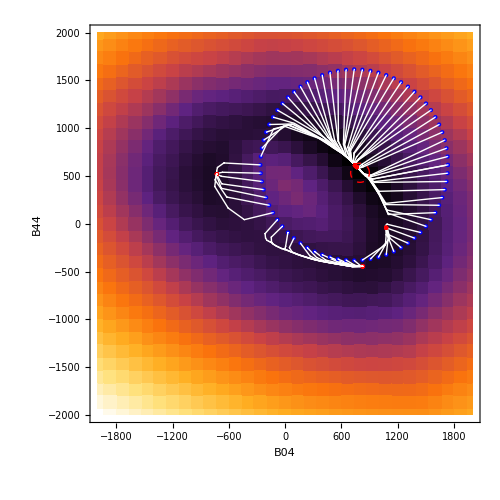

```mathematica
landscape=Flatten[landscapes[problemVars][[1]],1];
bestIndex=Ordering[Last/@landscape,1][[1]];
ListDensityPlot[landscape,InterpolationOrder->0,ColorFunction->"SunsetColors",Epilog->{{{Blue,Point[#[[1]]]},{Red,Point[#[[-1]]]},{White,Line[#]}}&/@histories,
{Red,Dashed,Circle[landscape[[bestIndex]][[;;2]],100]}
},FrameLabel->problemVars,ImageSize->500]
```

```mathematica
histories={};
best=standardValues[[problemVarsPositions]]//N;
solutions={};
Do[
history={};
problemVarsWithStartValues=Transpose[{problemVars,best+1000*{Cos[β],Sin[β]}}];
sol=FindMinimum[
Sum[(expData[[j]][[1]]-PartialHamEigenvalues[B04,B44][j])^2,{j,presentDataIndices}],
problemVarsWithStartValues,
Method->"LevenbergMarquardt",
MaxIterations->2000,
EvaluationMonitor:>(
history=Append[history,problemVars]
)
];
histories=Append[histories,history];
solutions=Append[solutions,(β->sol)];
,
{β,0,360 Degree,5 Degree}
];
```

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of FindMinimum::sszero will be suppressed during this calculation.

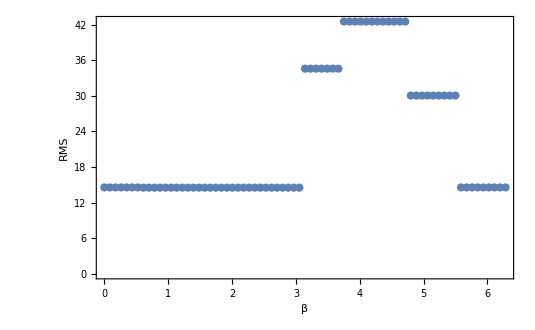

```mathematica
ListPlot[{First[#],Sqrt[Last[#][[1]]]/(√Length[presentDataIndices])}&/@solutions,Frame->True,FrameLabel->{"β","RMS"}]
```

```mathematica
ListPlot3D[landscape]
```

-Graphics3D-

```mathematica
GradientLine[pts_List,color_]:=(
numPoints=Length[pts];
times=Subdivide[0,1,100]//N;
path=Transpose[{Subdivide[0,1,numPoints-1],pts}];
superPoints=Interpolation[path][times];
dxs=Norm/@Prepend[Differences[superPoints],{0,0}];
lineIntegral=Accumulate[dxs];
lineIntegral=lineIntegral/lineIntegral[[-1]];
linePath=Transpose[{lineIntegral,times}];
evenTimes=Interpolation[linePath][times];
evenPoints=Interpolation[superPoints][evenTimes];
Table[{color,
CapForm["Round"],
Opacity[(idx)/Length[superPoints]],
Thickness[0.02*idx/Length[superPoints]],
Line[superPoints[[idx;;idx+1]]]},{idx,1,Length[superPoints]-1}]
)
```

```mathematica
superP=GradientLine[Table[{Cos[β],2*Sin[β]},{β,0,2π,0.01}],Blue];
dxs=Norm/@Prepend[Differences[superP],{0,0}];
```

```mathematica
Length[dxs]
```

101

```mathematica
Interpolation[{{0,{0,0}},{1,{1,1}}}]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

InterpolatingFunction[…]

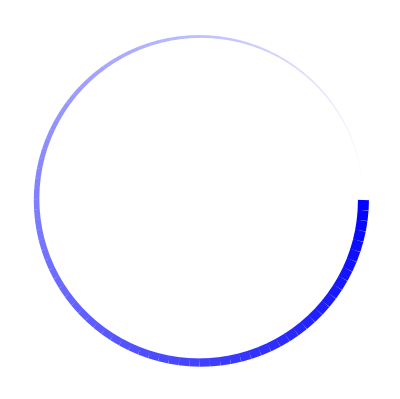

```mathematica
GradientLine[Table[{Cos[β],Sin[β]},{β,0,2π,0.01}],Blue]//Graphics
```

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

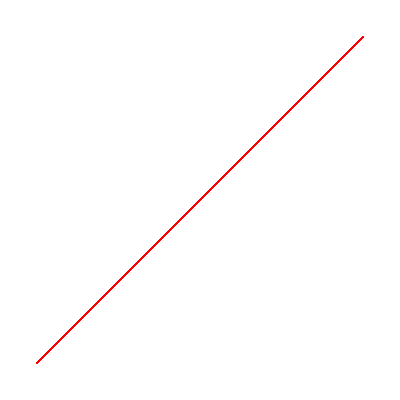

```mathematica
GradientLine[{{0,0},{1,1}},Red]//Graphics
```

```mathematica
ListPlot3D[landscape]
```

-Graphics3D-